# How does joint evolution of consumer traits affect resource specialization? Paula Vasconcelos & Claus Rueffler* *corresponding author: claus.rueffler@ebc.uu.se Notebook accompanying the paper with the same title published in The American Naturalist in 2019

```mathematica
ClearAll["Global`*"]
```

## Ecology (need not to be evaluated)

#### Population dynamical equilibria

The ODE-system given in Eq. (1) in the main part of the article and its interior equilibrium given by Eq. (A1) in the online appendix.

```mathematica
R1eq=r1 R1(1-R1/k1)-((e1 R1 Cr)/(1+h1 e1 R1+h2 e2 R2));
R2eq=r2 R2(1-R2/k2)-((e2 R2 Cr)/(1+h1 e1 R1+h2 e2 R2));
Creq=α1 e1 R1 Cr/(1+h1 e1 R1+h2 e2 R2)+α2 e2 R2 Cr/(1+h1 e1 R1+h2 e2 R2)-d Cr;
R1eq0 =R1eq==0;
R2eq0=R2eq==0;
Creq0=Creq==0;
Equilib=Solve[{R1eq0,R2eq0,Creq0,R1≠0,R2≠0,Cr≠0},{R1,R2,Cr}];
EquilibPos=Equilib[[1]]//FullSimplify
```

{R1→(k1 (d e2^2 h2 k2 r1-d e1 (1+e2 h2 k2) r2+e2 k2 (-e2 r1+e1 r2) α2))/(d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2),R2→-(k2 (d e2 (r1+e1 h1 k1 r1)-d e1^2 h1 k1 r2+e1 k1 (-e2 r1+e1 r2) α1))/(d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2),Cr→-(r1 r2 (d+d e1 h1 k1+d e2 h2 k2-e1 k1 α1-e2 k2 α2) (e2^2 k2 r1 α2+e1 e2^2 k1 k2 r1 (-h2 α1+h1 α2)+e1^2 k1 r2 (α1+e2 h2 k2 α1-e2 h1 k2 α2)))/((d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2)^2)}

Equilibrium under complete symmetry as shown in Eq. (A2) in the appendix.

```mathematica
EquilibPos/.completeSymmetry//FullSimplify
```

{R1→-d/(2 d e h-2 e α),R2→-d/(2 d e h-2 e α),Cr→-(r α (d+2 d e h k-2 e k α))/(2 e^2 k (-d h+α)^2)}

Numerical example

```mathematica
%/.{e->1/2,d->3/2,h->1/2,α->1,k->13,r->1}
```

{R1→6,R2→6,Cr→56/13}

#### Resource equilibria if only e evolves

```mathematica
EquilibPose={R1,R2,Cr}/.EquilibPos/.{h1->h,h2->h,α1->α,α2->α}/.symParEcol//FullSimplify (* Eq. (B1) in the appendix *)
```

{(-e1 e2 k+e2^2 k+(d e1)/(-d h+α))/(e1^2+e2^2),(e1 (e1-e2) k+(d e2)/(-d h+α))/(e1^2+e2^2),(r α (-d (1+(e1+e2) h k)+(e1+e2) k α))/((e1^2+e2^2) k (-d h+α)^2)}

The following calculation shows that the derivative of the resource equilibria with respect to the resident trait equals zero at the consumer extinction boundary given by 2ek(α-hd)=0. This makes intuitive sense: when the consumer population has zero density changing its feeding efficiency has not effect on the resource.

The equilibrium with feeding efficiencies written as functions.

```mathematica
{(-e1[θe] e2[θe] k+e2[θe]^2 k+(d e1[θe])/(-d h+α))/(e1[θe]^2+e2[θe]^2),(e1[θe] (e1[θe]-e2[θe]) k+(d e2[θe])/(-d h+α))/(e1[θe]^2+e2[θe]^2),(r α (-d (1+(e1[θe]+e2[θe]) h k)+(e1[θe]+e2[θe]) k α))/((e1[θe]^2+e2[θe]^2) k (-d h+α)^2)}
```

```mathematica
D[(-e1[θe] e2[θe] k+e2[θe]^2 k+(d e1[θe])/(-d h+α))/(e1[θe]^2+e2[θe]^2),θe]/.{e1'[θe]->e',e2'[θe]->-e'}/.esym//Simplify (* Eq. (B5) in the appendix *)
```

((-2 e k+d/(-d h+α)) e')/(2 e^2)

This derivative equals zero if 2ek(α-hd)=0 holds.

Under what conditions is resource 1 more abundant than resource 2? This result is shown as Eq. (B6) in the appendix.

```mathematica
EquilibPosE[[1]]>EquilibPosE[[2]]//Simplify
```

(e1-e2) (e1^2+e2^2) (d h-α) (d (1+e1 h k+e2 h k)-(e1+e2) k α)<0

Numerical example: abundance of resources and the consumer as a function of the specialization coefficient θe.

```mathematica
EquilibPosE/.{e1->te1,e2->te2}/.{r->1,k->9.5,d->1,h->1.8,α->2,ze->5}
```

{(5. te1-9.5 te1 te2+9.5 te2^2)/(te1^2+te2^2),(9.5 te1 (te1-te2)+5. te2)/(te1^2+te2^2),(5.26316 (-1+1.9 (te1+te2)))/(te1^2+te2^2)}

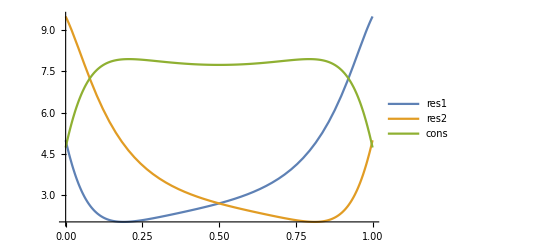

```mathematica
Plot[EquilibPosE/.{e1->te1,e2->te2}/.{r->1,k->9.5,d->1,h->1.8,α->2,ze->5}//Evaluate,{θe,0,1},PlotLegends->{"res1","res2","cons"}]
```

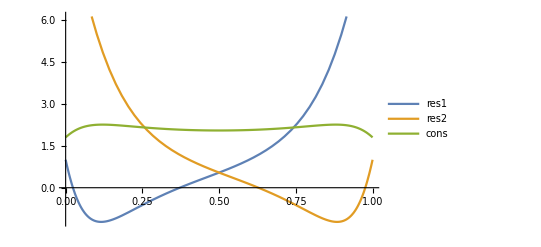

```mathematica
Plot[EquilibPosE/.{e1->te1,e2->te2}/.{r->1,k->10,d->1,h->1,α->2,ze->5}//Evaluate,{θe,0,1},PlotLegends->{"res1","res2","cons"}]
```

#### Resource equilibria as a function of the degree of specialization in handling time

```mathematica
EquilibPosh={R1,R2,Cr}/.EquilibPos//FullSimplify
```

{(k1 (d e2^2 h2 k2 r1-d e1 (1+e2 h2 k2) r2+e2 k2 (-e2 r1+e1 r2) α2))/(d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2),-(k2 (d e2 (r1+e1 h1 k1 r1)-d e1^2 h1 k1 r2+e1 k1 (-e2 r1+e1 r2) α1))/(d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2),-(r1 r2 (d+d e1 h1 k1+d e2 h2 k2-e1 k1 α1-e2 k2 α2) (e2^2 k2 r1 α2+e1 e2^2 k1 k2 r1 (-h2 α1+h1 α2)+e1^2 k1 r2 (α1+e2 h2 k2 α1-e2 h1 k2 α2)))/((d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2)^2)}

Abundance of resources and the consumer as a function of the specialization coefficient θh.

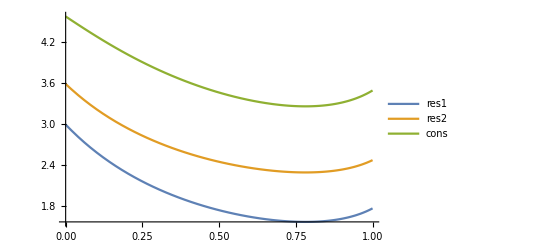

```mathematica
Plot[EquilibPosh/.{h1->th1,h2->th2}/.{r1->1.6,r2->1.6,k1->9.5,k2->9.5,d->1.5,e1->1.1,e2->1,α1->1,α2->1,zh->0.5}//Evaluate,{θh,0,1},PlotLegends->{"res1","res2","cons"}]
```

This figure indicates that changes in handling time affect the resource equilibria in the same way in the sense that either both resources are increasing or decreasing. Note that the feeding efficiencies are asymmetric. This causes that the equilibria of the two resources are not identical.

## Preliminaries (evaluate)

#### Replacement rules

```mathematica
sS={θem->θe,θhm->θh,θαm->θα};
completeSymmetry={r1->r,r2->r,k1->k,k2->k,e1->e,e2->e,h1->h,h2->h,α1->α,α2->α};
symParEcol={r1->r,r2->r,k1->k,k2->k};
singpt={θe->1/2,θh->1/2,θα->1/2};
esym={e1[θem]->e,e2[θem]->e,e1[θe]->e,e2[θe]->e,e1->e,e2->e};
αsym={α1[θαm]->α,α2[θαm]->α,α1[θα]->α,α2[θα]->α,α1->α,α2->α};
hsym={h1[θhm]->h,h2[θhm]->h,h1[θh]->h,h2[θh]->h,h1->h,h2->h};
symtraits={e1->e,e2->e,h1->h,h2->h,α1->α,α2->α};
TradeOffsEHsp={e->te1,h->th1};
TradeOffsEAsp={e->te1,α->tα1};
TradeOffsHAsp={h->th1,α->tα1};
TradeOffsEHAsp={e->te1,h->th1,α->tα1};
derivatives={e'->de,e''->dde,h'->dh,h''->ddh,α'->dα,α''->ddα,R->Rsym,R'->d1R,Derivative[1,0][R]->d1R,Derivative[1,0,0][R]->d1R};
rese={R1[θe,θh,θα]->R1[θe],R2[θe,θh,θα]->R2[θe]};
resh={R1[θe,θh,θα]->R1[θh],R2[θe,θh,θα]->R2[θh]};
resα={R1[θe,θh,θα]->R1[θα],R2[θe,θh,θα]->R2[θα]};
reseh={R1[θe,θh,θα]->R1[θe,θh],R2[θe,θh,θα]->R2[θe,θh],α1[θαm]->α,α2[θαm]->α};
resαh={R1[θe,θh,θα]->R1[θα,θh],R2[θe,θh,θα]->R2[θα,θh],e1[θem]->e,e2[θem]->e};
reseα={R1[θe,θh,θα]->R1[θe,θα],R2[θe,θh,θα]->R2[θe,θα],h1[θhm]->h,h2[θhm]->h};
```

#### Trade-off parametrization

```mathematica
te1=(1-E^(-ze (1- θe)))/(1-E^(-ze));
te2=(1-E^(-ze θe))/(1-E^(-ze));
te1m=te1/.θe->θem;
te2m=te2/.θe->θem;
tα1=(1-E^(-zα (1- θα)))/(1-E^(-zα));
tα2=(1-E^(-zα θα))/(1-E^(-zα));
tα1m=tα1/.θα->θαm;
tα2m=tα2/.θα->θαm;
th1=1-((1-E^(-zh (1- θh)))/(1-E^(-zh)));
th2=1-((1-E^(-zh θh))/(1-E^(-zh)));
th1m=th1/.θh->θhm;
th2m=th2/.θh->θhm;
```

#### Population dynamical equilibria

```mathematica
R1eq=r1 R1(1-R1/k1)-((e1 R1 Cr)/(1+h1 e1 R1+h2 e2 R2));
R2eq=r2 R2(1-R2/k2)-((e2 R2 Cr)/(1+h1 e1 R1+h2 e2 R2));
Creq=α1 e1 R1 Cr/(1+h1 e1 R1+h2 e2 R2)+α2 e2 R2 Cr/(1+h1 e1 R1+h2 e2 R2)-d Cr;
R1eq0 =R1eq==0;
R2eq0=R2eq==0;
Creq0=Creq==0;
Equilib=Solve[{R1eq0,R2eq0,Creq0,R1≠0,R2≠0,Cr≠0},{R1,R2,Cr}];
EquilibPos=Equilib[[1]]//FullSimplify
```

{R1→(k1 (d e2^2 h2 k2 r1-d e1 (1+e2 h2 k2) r2+e2 k2 (-e2 r1+e1 r2) α2))/(d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2),R2→-(k2 (d e2 (r1+e1 h1 k1 r1)-d e1^2 h1 k1 r2+e1 k1 (-e2 r1+e1 r2) α1))/(d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2),Cr→-(r1 r2 (d+d e1 h1 k1+d e2 h2 k2-e1 k1 α1-e2 k2 α2) (e2^2 k2 r1 α2+e1 e2^2 k1 k2 r1 (-h2 α1+h1 α2)+e1^2 k1 r2 (α1+e2 h2 k2 α1-e2 h1 k2 α2)))/((d e2^2 h2 k2 r1+d e1^2 h1 k1 r2-e1^2 k1 r2 α1-e2^2 k2 r1 α2)^2)}

#### Invasion fitness

Invasion Fitness with implicit resources.

```mathematica
S=(α1[θαm] e1[θem] R1[θe,θh,θα]+α2[θαm] e2[θem] R2[θe,θh,θα])/(1+e1[θem] h1[θhm] R1[θe,θh,θα]+e2[θem] h2[θhm] R2[θe,θh,θα])-d
```

-d+(e1[θem] R1[θe,θh,θα] α1[θαm]+e2[θem] R2[θe,θh,θα] α2[θαm])/(1+e1[θem] h1[θhm] R1[θe,θh,θα]+e2[θem] h2[θhm] R2[θe,θh,θα])

## Evolution

Note : All matrices are evaluated at the symmetric singular point.

Evolution of the traits separately

## Evolution of feeding efficiency e

Invasion fitness for the case that only e evolves

```mathematica
Se=S/.rese/.{h1[θhm]->h,h2[θhm]->h, α1[θαm]->α, α2[θαm]->α}
```

-d+(α e1[θem] R1[θe]+α e2[θem] R2[θe])/(1+h e1[θem] R1[θe]+h e2[θem] R2[θe])

Gradient for feeding efficiency when evolving in isolation.

```mathematica
D[Se,θem]//Simplify
```

(α (R1[θe] e1'[θem]+R2[θe] e2'[θem]))/(1+h e1[θem] R1[θe]+h e2[θem] R2[θe])^2

```mathematica
grade=(α (R1[θe] e1'[θem]+R2[θe] e2'[θem]))/(1+h e1[θem] R1[θe]+h e2[θem] R2[θe])^2; (* Eq. B2 *)
```

Hessian and Jacobian matrices evaluated at the symmetric singular point.

```mathematica
he=D[Se,θem,θem]/.sS/.singpt/.{R1[1/2]->R,R2[1/2]->R,e1[1/2]->e,e2[1/2]->e,e1'[1/2]->e',e2'[1/2]->-e',e1''[1/2]->e'',e2''[1/2]->e''}//Simplify
qe=D[Se,θem,θe]/.sS/.singpt/.{R1[1/2]->R,R2[1/2]->R,R1'[1/2]->R',R2'[1/2]->-R',e1[1/2]->e,e2[1/2]->e,e1'[1/2]->e',e2'[1/2]->-e'}//Simplify
je=he+qe//Simplify
```

(2 R α e'')/(1+2 e h R)^2

(2 α e' R')/(1+2 e h R)^2

(2 α (e' R'+R e''))/(1+2 e h R)^2

```mathematica
He=(2 R α e'')/(1+2 e h R)^2; (* Eq. B7 *)
Je=(2 α (e' R'+R e''))/(1+2 e h R)^2;  (* Eq. B8 *)
```

## Evolution of handling time h

Invasion fitness for the case that only h evolves

```mathematica
Sh=S/.resh/.{e1[θem]->e,e2[θem]->e, α1[θαm]->α, α2[θαm]->α}
```

-d+(e α R1[θh]+e α R2[θh])/(1+e h1[θhm] R1[θh]+e h2[θhm] R2[θh])

Gradient for handling time, general.

```mathematica
D[Sh,θhm]/.sS//FullSimplify
```

-(e^2 α (R1[θh]+R2[θh]) (R1[θh] h1'[θh]+R2[θh] h2'[θh]))/(1+e h1[θh] R1[θh]+e h2[θh] R2[θh])^2

```mathematica
gradh=-(e^2 α (R1[θh]+R2[θh]) (R1[θh] h1'[θh]+R2[θh] h2'[θh]))/(1+e h1[θh] R1[θh]+e h2[θh] R2[θh])^2; (* Eq. B10 *)
```

Hessian and Jacobian matrices evaluated at the symmetric singular point.

```mathematica
hh=D[Sh,θhm,θhm]/.sS/.singpt/.{R1[1/2]->R,R2[1/2]->R,h1[1/2]->h,h2[1/2]->h,h1'[1/2]->h',h2'[1/2]->-h',h1''[1/2]->h'',h2''[1/2]->h''}//Simplify
qh=D[Sh,θhm,θh]/.sS/.singpt/.{R1[1/2]->R,R2[1/2]->R,R1'[1/2]->R',R2'[1/2]->R',h1[1/2]->h,h2[1/2]->h,h1'[1/2]->h',h2'[1/2]->-h'}//Simplify
jh=hh+qh//Simplify
```

-(4 e^2 R^2 α h'')/(1+2 e h R)^2

0

-(4 e^2 R^2 α h'')/(1+2 e h R)^2

```mathematica
Hh=-(4 e^2 R^2 α h'')/(1+2 e h R)^2; (* Eq. B13 *)
Jh=-(4 e^2 R^2 α h'')/(1+2 e h R)^2;
```

## Evolution of conversion efficiency α

Invasion fitness for the case that only α evolves

```mathematica
Sα=S/.rese/.{e1[θem]->e,e2[θem]->e, h1[θhm]->h, h2[θhm]->h}
```

-d+(e R1[θe] α1[θαm]+e R2[θe] α2[θαm])/(1+e h R1[θe]+e h R2[θe])

Gradient for conversion efficiency, general.

```mathematica
D[Sα,θαm]/.sS//FullSimplify
```

(e (R1[θe] α1'[θα]+R2[θe] α2'[θα]))/(1+e h (R1[θe]+R2[θe]))

```mathematica
gradα=(e (R1[θe] α1'[θα]+R2[θe] α2'[θα]))/(1+e h (R1[θe]+R2[θe])); (* Eq. B16 *)
```

Hessian and Jacobian matrices evaluated at the symmetric singular point.

```mathematica
hα=D[Sα,θαm,θαm]/.sS/.singpt/.{R1[1/2]->R,R2[1/2]->R,α1[1/2]->α,α2[1/2]->α,α1'[1/2]->α',α2'[1/2]->-α',α1''[1/2]->α'',α2''[1/2]->α''}//Simplify
qα=D[Sα,θαm,θα]/.sS/.singpt/.{R1[1/2]->R,R2[1/2]->R,R1'[1/2]->R',R2'[1/2]->R',α1[1/2]->α,α2[1/2]->α,α1'[1/2]->α',α2'[1/2]->-α'}//Simplify
jα=hα+qα//Simplify
```

(2 e R α'')/(1+2 e h R)

0

(2 e R α'')/(1+2 e h R)

```mathematica
Hα=(2 e R α'')/(1+2 e h R); (* Eq. B19 *)
Jα=(2 e R α'')/(1+2 e h R);
```

Joint trait evolution

## Joint evolution of feeding efficiency and handling time

### Analytical results

Invasion fitness

```mathematica
Seh=S/.reseh
```

-d+(α e1[θem] R1[θe,θh]+α e2[θem] R2[θe,θh])/(1+e1[θem] h1[θhm] R1[θe,θh]+e2[θem] h2[θhm] R2[θe,θh])

Fitness gradient

```mathematica
D[Seh,θem]/.{θem->θe,θhm->θh}//Simplify (* Eq. C1a *)
D[Seh,θhm]/.{θem->θe,θhm->θh}//Simplify (* Eq. C1b *)
```

(α (R2[θe,θh] e2'[θe]+R1[θe,θh] ((1+e2[θe] (-h1[θh]+h2[θh]) R2[θe,θh]) e1'[θe]+e1[θe] (h1[θh]-h2[θh]) R2[θe,θh] e2'[θe])))/(1+e1[θe] h1[θh] R1[θe,θh]+e2[θe] h2[θh] R2[θe,θh])^2

-(α (e1[θe] R1[θe,θh]+e2[θe] R2[θe,θh]) (e1[θe] R1[θe,θh] h1'[θh]+e2[θe] R2[θe,θh] h2'[θh]))/(1+e1[θe] h1[θh] R1[θe,θh]+e2[θe] h2[θh] R2[θe,θh])^2

Hessian

```mathematica
h11=D[Seh,{θem,2}];
h12=D[Seh,θem,θhm];
h22=D[Seh,{θhm,2}];
{{h11,h12},{h12,h22}}/.sS/.singpt/.symParEcol/.{R1[1/2,1/2]->R,R2[1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,e1'[1/2]->e',e2'[1/2]->-e',h1'[1/2]->h',h2'[1/2]->-h',e1''[1/2]->e'',e2''[1/2]->e'',h1''[1/2]->h'',h2''[1/2]->h''}//Simplify
```

{{(2 R α e'')/(1+2 e h R)^2,-(4 e R^2 α e' h')/(1+2 e h R)^2},{-(4 e R^2 α e' h')/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

```mathematica
Heh={{(2 R α e'')/(1+2 e h R)^2,-(4 e R^2 α e' h')/(1+2 e h R)^2},{-(4 e R^2 α e' h')/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}; (* Eq. C6 *)
```

```mathematica
Det[Heh]//Simplify
```

-(8 e^2 R^3 α^2 (2 R (e')^2 (h')^2+e'' h''))/(1+2 e h R)^4

```mathematica
DetHeh=-(8 e^2 R^3 α^2 (2 R (e')^2 (h')^2+e'' h''))/(1+2 e h R)^4;
```

```mathematica
Eigensystem[Heh]//FullSimplify
```

{{-(R α (-e''+2 e^2 R h''+√(16 e^2 R^2 (e')^2 (h')^2+(e''+2 e^2 R h'')^2)))/(1+2 e h R)^2,(R α (e''-2 e^2 R h''+√(16 e^2 R^2 (e')^2 (h')^2+(e''+2 e^2 R h'')^2)))/(1+2 e h R)^2},{{(-e''-2 e^2 R h''+√(16 e^2 R^2 (e')^2 (h')^2+(e''+2 e^2 R h'')^2))/(4 e R e' h'),1},{-(e''+2 e^2 R h''+√(16 e^2 R^2 (e')^2 (h')^2+(e''+2 e^2 R h'')^2))/(4 e R e' h'),1}}}

```mathematica
EigenvectorHeh={-(e''+2 e^2 R h''+√(16 e^2 R^2 (e')^2 (h')^2+(e''+2 e^2 R h'')^2))/(4 e R e' h'),1};
```

Q-matrix

```mathematica
q11=D[Seh,θem,θe];
q12=D[Seh,θem,θh];
q21=D[Seh,θhm,θe];
q22=D[Seh,θhm,θh];
{{q11,q12},{q21,q22}}/.sS/.singpt/.symParEcol/.{R1[1/2,1/2]->R,R2[1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,e1'[1/2]->e',e2'[1/2]->-e',h1'[1/2]->h',h2'[1/2]->-h',Derivative[1,0][R1][1/2,1/2]->Derivative[1,0][R],Derivative[1,0][R2][1/2,1/2]->-Derivative[1,0][R],Derivative[0,1][R1][1/2,1/2]->Derivative[0,1][R],Derivative[0,1][R2][1/2,1/2]->Derivative[0,1][R]}//Simplify
```

{{(2 α e' R^(1,0))/(1+2 e h R)^2,0},{-(4 e^2 R α h' R^(1,0))/(1+2 e h R)^2,0}}

```mathematica
Qeh={{(2 α e' Derivative[1,0][R])/(1+2 e h R)^2,0},{-(4 e^2 R α h' Derivative[1,0][R])/(1+2 e h R)^2,0}}; (* Eq. C7 *)
```

Jacobian matrix

```mathematica
Heh+Qeh//Simplify
```

{{(2 α (R e''+e' R^(1,0)))/(1+2 e h R)^2,-(4 e R^2 α e' h')/(1+2 e h R)^2},{-(4 e R α h' (R e'+e R^(1,0)))/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

```mathematica
Jeh={{(2 α (R e''+e' Derivative[1,0][R]))/(1+2 e h R)^2,-(4 e R^2 α e' h')/(1+2 e h R)^2},{-(4 e R α h' (R e'+e Derivative[1,0][R]))/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
```

```mathematica
Det[Jeh]//FullSimplify
```

-(8 e^2 R^2 α^2 (2 R^2 (e')^2 (h')^2+R e'' h''+e' (2 e R (h')^2+h'') R^(1,0)))/(1+2 e h R)^4

```mathematica
DetJeh=-(8 e^2 R^2 α^2 (2 R^2 (e')^2 (h')^2+R e'' h''+e' (2 e R (h')^2+h'') Derivative[1,0][R]))/(1+2 e h R)^4;
```

```mathematica
Tr[Jeh]//FullSimplify;
```

```mathematica
trJeh=(2 α (R (e''-2 e^2 R h'')+e' Derivative[1,0][R]))/(1+2 e h R)^2;
```

Product of the Jacobian matrix of the fitness gradient and the mutational variance-covariance matrix M={{m11,m12},{m12,m22}}.  This equals the Jacobian matrix of the canonical equation (Eq. 6 in the main part of the paper). A singular point is an attractor of the evolutionary dynamics if both eigenvalues of this matrix have negative real parts.

```mathematica
JJeh={{m11,m12},{m12,m22}}.Jeh//FullSimplify
```

{{(2 α (e' (-2 e m12 R^2 h'+m11 R^(1,0))+R (m11 e''-2 e^2 m12 h' R^(1,0))))/(1+2 e h R)^2,-(4 e R^2 α (m11 e' h'+e m12 h''))/(1+2 e h R)^2},{(2 α (e' (-2 e m22 R^2 h'+m12 R^(1,0))+R (m12 e''-2 e^2 m22 h' R^(1,0))))/(1+2 e h R)^2,-(4 e R^2 α (m12 e' h'+e m22 h''))/(1+2 e h R)^2}}

```mathematica
Tr[JJeh]//FullSimplify
```

(2 α (m11 R e''+e' (-4 e m12 R^2 h'+m11 R^(1,0))-2 e^2 R (m22 R h''+m12 h' R^(1,0))))/(1+2 e h R)^2

```mathematica
trJJeh=(2 α (m11 R e''+e' (-4 e m12 R^2 h'+m11 Derivative[1,0][R])-2 e^2 R (m22 R h''+m12 h' Derivative[1,0][R])))/(1+2 e h R)^2;
```

Symmetric Jacobian

```mathematica
(Jeh+Transpose[Jeh])/2//Simplify
```

{{(2 α (R e''+e' R^(1,0)))/(1+2 e h R)^2,-(2 e R α h' (2 R e'+e R^(1,0)))/(1+2 e h R)^2},{-(2 e R α h' (2 R e'+e R^(1,0)))/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

```mathematica
Jsymeh={{(2 α (R e''+e' Derivative[1,0][R]))/(1+2 e h R)^2,-(2 e R α h' (2 R e'+e Derivative[1,0][R]))/(1+2 e h R)^2},{-(2 e R α h' (2 R e'+e Derivative[1,0][R]))/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}; (* Eq. C8 *)
```

```mathematica
Det[Jsymeh]//FullSimplify
```

-(4 e^2 R^2 α^2 (4 R^2 (e')^2 (h')^2+2 R e'' h''+2 e' (2 e R (h')^2+h'') R^(1,0)+e^2 (h')^2 (R^(1,0))^2))/(1+2 e h R)^4

```mathematica
DetJsymeh=-(4 e^2 R^2 α^2 (4 R^2 (e')^2 (h')^2+2 R e'' h''+2 e' (2 e R (h')^2+h'') Derivative[1,0][R]+e^2 (h')^2 (Derivative[1,0][R])^2))/(1+2 e h R)^4;
```

### Numerics

Summary of analytical results (needs to be evaluated for the numerical calculations)

```mathematica
Heh={{(2 R α e'')/(1+2 e h R)^2,-(4 e R^2 α e' h')/(1+2 e h R)^2},{-(4 e R^2 α e' h')/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
DetHeh=-(8 e^2 R^3 α^2 (2 R (e')^2 (h')^2+e'' h''))/(1+2 e h R)^4;
EigenvectorHeh={-(e''+2 e^2 R h''+√(16 e^2 R^2 (e')^2 (h')^2+(e''+2 e^2 R h'')^2))/(4 e R e' h'),1};
Qeh={{(2 α e' Derivative[1,0][R])/(1+2 e h R)^2,0},{-(4 e^2 R α h' Derivative[1,0][R])/(1+2 e h R)^2,0}};
Jeh={{(2 α (R e''+e' Derivative[1,0][R]))/(1+2 e h R)^2,-(4 e R^2 α e' h')/(1+2 e h R)^2},{-(4 e R α h' (R e'+e Derivative[1,0][R]))/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
DetJeh=-(8 e^2 R^2 α^2 (2 R^2 (e')^2 (h')^2+R e'' h''+e' (2 e R (h')^2+h'') Derivative[1,0][R]))/(1+2 e h R)^4;
trJeh=(2 α (R (e''-2 e^2 R h'')+e' Derivative[1,0][R]))/(1+2 e h R)^2;
trJJeh=(2 α (m11 R e''+e' (-4 e m12 R^2 h'+m11 Derivative[1,0][R])-2 e^2 R (m22 R h''+m12 h' Derivative[1,0][R])))/(1+2 e h R)^2;
Jsymeh={{(2 α (R e''+e' Derivative[1,0][R]))/(1+2 e h R)^2,-(2 e R α h' (2 R e'+e Derivative[1,0][R]))/(1+2 e h R)^2},{-(2 e R α h' (2 R e'+e Derivative[1,0][R]))/(1+2 e h R)^2,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
DetJsymeh=-(4 e^2 R^2 α^2 (4 R^2 (e')^2 (h')^2+2 R e'' h''+2 e' (2 e R (h')^2+h'') Derivative[1,0][R]+e^2 (h')^2 (Derivative[1,0][R])^2))/(1+2 e h R)^4;
```

#### Bifurcation plots

```mathematica
Clear[d,k,α]
```

```mathematica
de=D[te1,θe];
dde=D[te1,θe,θe];
dh=D[th1,θh];
ddh=D[th1,θh,θh];
Rsym=R1/.EquilibPos[[1]]/.symParEcol/.symtraits//FullSimplify;
R1=R1/.EquilibPos[[1]]/.symParEcol/.{e1->te1,e2->te2}/.symtraits//Simplify;
d1R=D[R1,θe]/.singpt//FullSimplify;
```

```mathematica
ConsExehEva=2 e k(α-h d)-d/.TradeOffsEHsp/.singpt (* existence region of the consumer *)
stabeh=(α+h d)/(α-h d)-2 e h k/.TradeOffsEHsp/.singpt; (* stability boundary for the population dynamics *)
DetHehEva=DetHeh/.derivatives/.TradeOffsEHsp/.singpt;
DetJehEva=DetJeh/.derivatives/.TradeOffsEHsp/.singpt;
trJehEva=trJeh/.derivatives/.TradeOffsEHsp/.singpt;
trJJehEva=trJJeh/.derivatives/.TradeOffsEHsp/.singpt;
JsymehEva=Jsymeh/.derivatives/.TradeOffsEHsp/.singpt;
DetJsymehEva=DetJsymeh/.derivatives/.TradeOffsEHsp/.singpt;
```

-d+(2 (1-ⅇ^(-ze/2)) k (-d (1-(1-ⅇ^(-zh/2))/(1-ⅇ^-zh))+α))/(1-ⅇ^-ze)

```mathematica
d=.9;k=2.5;α=1; (* parameters used for Fig. 5 in the main part of the paper *)
```

```mathematica
(*d=.3;k=1.6;α=1.2; (* parameters used for Fig. E3 produce a small area with a Garden of Eden *)
```

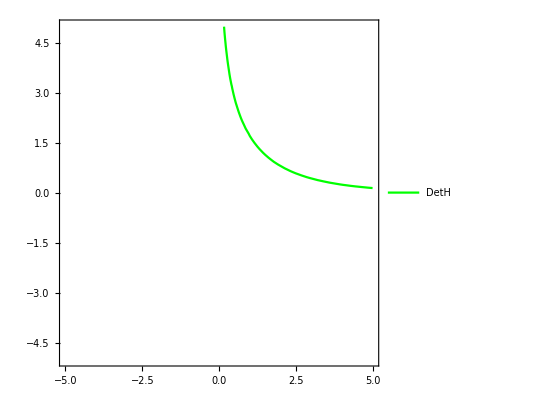

```mathematica
DetHehCont=ContourPlot[DetHehEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},RegionFunction->Function[{ze,zh},-d+(2 (1-ⅇ^(-ze/2)) k (-d (1-(1-ⅇ^(-zh/2))/(1-ⅇ^-zh))+α))/(1-ⅇ^-ze)>=0],ContourShading->None,ContourStyle->{Green},PlotLegends->{"DetH"}]
```

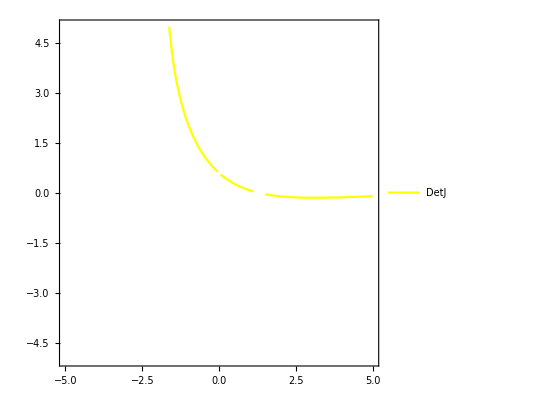

```mathematica
DetJConteh=ContourPlot[DetJehEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},RegionFunction->Function[{ze,zh},-d+(2 (1-ⅇ^(-ze/2)) k (-d (1-(1-ⅇ^(-zh/2))/(1-ⅇ^-zh))+α))/(1-ⅇ^-ze)>=0],ContourShading->None,ContourStyle->{Yellow},PlotLegends->{"DetJ"}]
```

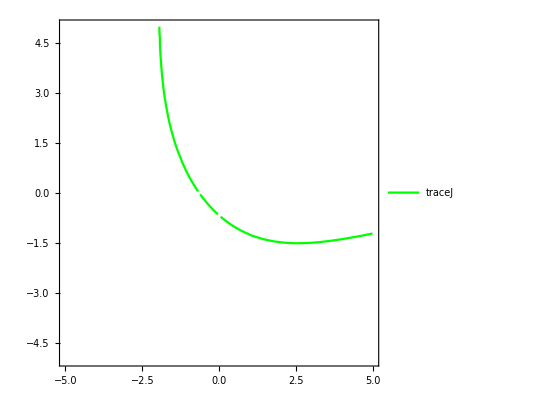

```mathematica
trJConteh=ContourPlot[trJehEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},ContourShading->None,ContourStyle->{Green},PlotLegends->{"traceJ"}]
```

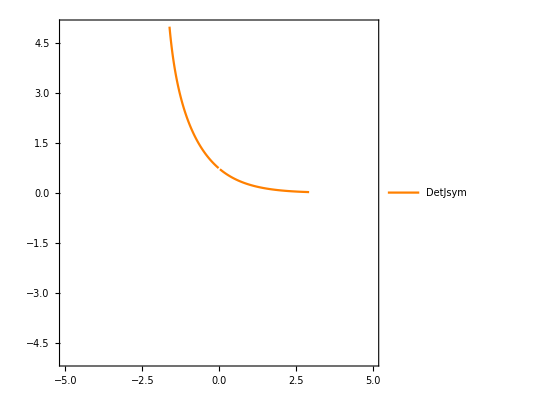

```mathematica
DetJsymConteh=ContourPlot[DetJsymehEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},RegionFunction->Function[{ze,zh},-d+(2 (1-ⅇ^(-ze/2)) k (-d (1-(1-ⅇ^(-zh/2))/(1-ⅇ^-zh))+α))/(1-ⅇ^-ze)>=0],ContourShading->None,ContourStyle->{Orange},PlotPoints->101,PlotLegends->{"DetJsym"}]
```

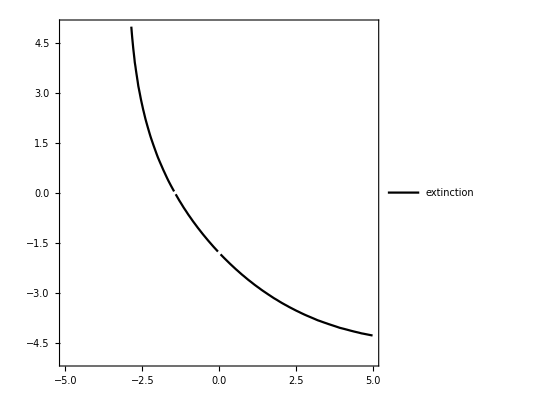

```mathematica
exConteh=ContourPlot[ConsExehEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},ContourShading->None,ContourStyle->{Black},PlotLegends->{"extinction"}]
```

```mathematica
stabCont=ContourPlot[stabeh,{ze,-5,5},{zh,-5,5},Contours->{0},Exclusions->"Discontinuities",ContourShading->None,ContourStyle->{Pink},PlotLegends->{"stability"}]
```

-Graphics-

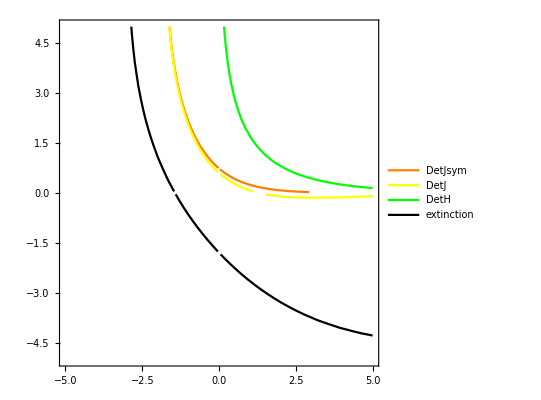

```mathematica
Show[DetJsymConteh,DetJConteh,DetHehCont,exConteh] (* Figure 5a *)
```

The following graph gives the output for the parameters d=0.3, k=1.6 and α=1.2 as used for Figure E3.

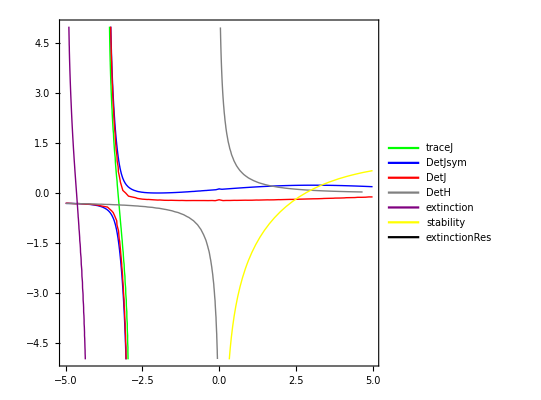

```mathematica
Show[trJConteh,DetJsymConteh,DetJConteh,DetHessConteh,exCont2D,stabCont]
```

#### Stream plots

```mathematica
Seh
```

-d+(α e1[θem] R1[θe,θh]+α e2[θem] R2[θe,θh])/(1+e1[θem] h1[θhm] R1[θe,θh]+e2[θem] h2[θhm] R2[θe,θh])

```mathematica
streameh={e1[θe]->e1,e2[θe]->e2,e1'[θe]->de1,e2'[θe]->de2,h1[θh]->h1,h2[θh]->h2,h1'[θh]->dh1,h2'[θh]->dh2,R1[θe,θh]->R1,R2[θe,θh]->R2,e'->de1,h'->dh1,e''->ddesym,h''->ddhsym,Derivative[1,0][R]->d1R};
gradeh={{m11,m12},{m12,m22}}.{D[Seh,θem],D[Seh,θhm]}/.sS/.streameh//FullSimplify
```

{-((de2 m11 (-1+e1 (-h1+h2) R1) R2+dh1 e1 m12 R1 (e1 R1+e2 R2)+dh2 e2 m12 R2 (e1 R1+e2 R2)+de1 m11 R1 (-1+e2 (h1-h2) R2)) α)/(1+e1 h1 R1+e2 h2 R2)^2,-((de2 m12 (-1+e1 (-h1+h2) R1) R2+dh1 e1 m22 R1 (e1 R1+e2 R2)+dh2 e2 m22 R2 (e1 R1+e2 R2)+de1 m12 R1 (-1+e2 (h1-h2) R2)) α)/(1+e1 h1 R1+e2 h2 R2)^2}

```mathematica
traitseh={e1->te1,e2->te2,h1->th1,h2->th2,e->te1,h->th1,R->R1};
de1=D[te1,θe];
de2=D[te2,θe];
ddesym=D[te1,θe,θe]/.θe->0.5;
dh1=D[th1,θh];
dh2=D[th2,θh];
ddhsym=D[th1,θh,θh]/.θh->0.5;
R1=R1/.EquilibPos[[1]]/.symParEcol/.traitseh/.symtraits//Simplify;
R2=R2/.EquilibPos[[2]]/.symParEcol/.traitseh/.symtraits//Simplify;
d1R=D[R1,θe]/.singpt//FullSimplify;
gradehEva=gradeh/.traitseh;
trJJehEva=trJJeh/.streameh/.traitseh/.singpt;
```

```mathematica
m=FindInstance[trJJehEva>0&&m11 m22>m12^2&&m11>0&&m22>0&&m11==1/4&&m22==1,{m11,m12,m22}] (* finding a mutational variance-covariance matrix such that the trace of the Jacobian matrix of the canonical equation is positive *)
```

{{m11→0.25,m12→0.475487,m22→1.}}

```mathematica
m={m11->1/4,m12->.47,m22->1}; 
m11 m22>m12^2/.m
```

True

```mathematica
(* ze=0.4;zh=0.4; d=.9;k=2.5;α=1; m={m11->1, m12->0, m22->1}; parameters for Figure E2a *)
ze=0.4;zh=0.4;d=.9;k=2.5;α=1; (* parameters for Figure E2b *)
```

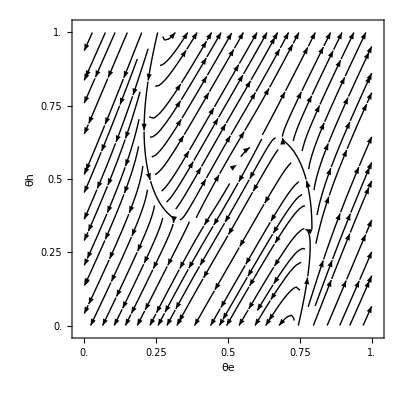

```mathematica
StreamPlot[gradehEva/.m,{θe,0,1},{θh,0,1},FrameLabel->{θe,θh},AspectRatio->1,LabelStyle->Directive[Bold,Black],StreamStyle->{Black,Black},StreamPoints->100,StreamScale->Large,FrameTicks->{{{0.0,0.25,0.5,0.75,1.0},None},{{0.0,0.25,0.5,0.75,1.0},None}}] (* Figure E2b *)
```

#### Branching conditions (iii) for weakly attracting points in Figure E3

Here, we deal with the branching condition (iii) of Geritz et al. (2016)  for the lower left region in Figure E3. This is done numerically for selected points in this region.
We choose zh=-0.6 and search for the interval of values ze such that detJ>0 and detJsym<0. Then J has two eigenvalues with positive real part while Jsym has a positive and a negative eigenvalue. For such combinations of trade-off curvatures it seems easy to find matrices M such that MJ has two eigenvalues with negative real part.

```mathematica
EigenvectorHehEva=EigenvectorHeh/.derivatives/.TradeOffsEHsp/.singpt; (* dominant eigenvector of the Hessian matrix *)
QehEva=Qeh/.derivatives/.TradeOffsEHsp/.singpt;(* Q-matrix *)
```

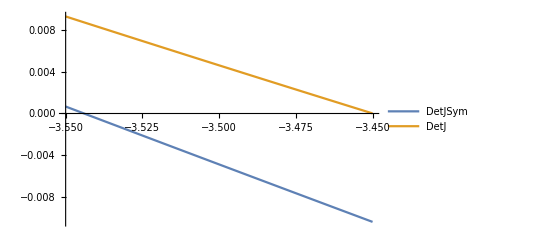

```mathematica
Clear[zh,ze]
d=.3;k=1.6;α=1.2; (* parameters used for Figure E3 *)
Plot[{DetJsymehEva,DetJehEva}/.{zh->-0.6}//Evaluate,{ze,-3.55,-3.45},PlotLegends->{"DetJSym","DetJ"}]
```

```mathematica
zh=-0.6;ze=-3.5; (* thus, ze=-3.5 fullfills our requirements *)
FindInstance[trJJehEva<0&&m11 m22>m12^2&&m11>0&&m22>0,{m11,m12,m22}] (* with this mutational variance-covariance matrix the weakly attracting singular point is indeed an attractor *)
m={{m11/.%[[1,1]],m12/.%[[1,2]]},{m12/.%[[1,2]],m22/.%[[1,3]]}}
u=EigenvectorHehEva/.{ze->-3.5,zh->-0.6} (* eigenvector corresponding to the dominant eigenvalue of the Hessian matrix *)
z=m.u (* vector giving the direction of branching *)
-z.QehEva.z>0 (* checking condition (iii) from Geritz et al. (2016) *)
```

{{m11→0.0556165,m12→-0.229867,m22→1.}}

{{0.0556165,-0.229867},{-0.229867,1.}}

{12.111,1}

{0.443706,-1.78393}

True

```mathematica
Clear[d,k,α,ze,zh]
```

## Joint evolution of feeding efficiency and conversion efficiency

### Analytical results

Invasion fitness

```mathematica
Seα=S/.reseα
```

-d+(e1[θem] R1[θe,θα] α1[θαm]+e2[θem] R2[θe,θα] α2[θαm])/(1+h e1[θem] R1[θe,θα]+h e2[θem] R2[θe,θα])

Fitness gradient

```mathematica
D[Seα,θem]/.{θem->θe,θαm->θα}//Simplify 
D[Seα,θαm]/.{θem->θe,θαm->θα}//Simplify
```

(R2[θe,θα] α2[θα] e2'[θe]+R1[θe,θα] (h R2[θe,θα] α2[θα] (-e2[θe] e1'[θe]+e1[θe] e2'[θe])+α1[θα] ((1+h e2[θe] R2[θe,θα]) e1'[θe]-h e1[θe] R2[θe,θα] e2'[θe])))/(1+h e1[θe] R1[θe,θα]+h e2[θe] R2[θe,θα])^2

(e1[θe] R1[θe,θα] α1'[θα]+e2[θe] R2[θe,θα] α2'[θα])/(1+h e1[θe] R1[θe,θα]+h e2[θe] R2[θe,θα])

Hessian

```mathematica
h11=D[Seα,{θem,2}];
h12=D[Seα,θem,θαm];
h22=D[Seα,{θαm,2}];
{{h11,h12},{h12,h22}}/.sS/.singpt/.{R1[1/2,1/2]->R,R2[1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,r1->r,r2->r,k1->k,k2->k,e1'[1/2]->e',e2'[1/2]->-e',α1'[1/2]->α',α2'[1/2]->-α',e1''[1/2]->e'',e2''[1/2]->e'',α1''[1/2]->α'',α2''[1/2]->α''}//Simplify
```

{{(2 R α e'')/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R)},{(2 R e' α')/(1+2 e h R),(2 e R α'')/(1+2 e h R)}}

```mathematica
Heα={{(2 R α e'')/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R)},{(2 R e' α')/(1+2 e h R),(2 e R α'')/(1+2 e h R)}};
```

```mathematica
Det[Heα]
```

-(4 R^2 (e')^2 (α')^2)/(1+2 e h R)^3-(8 e h R^3 (e')^2 (α')^2)/(1+2 e h R)^3+(4 e R^2 α e'' α'')/(1+2 e h R)^3

```mathematica
DetHeα=-(4 R^2 (e')^2 (α')^2)/(1+2 e h R)^3-(8 e h R^3 (e')^2 (α')^2)/(1+2 e h R)^3+(4 e R^2 α e'' α'')/(1+2 e h R)^3;
```

Q-matrix

```mathematica
q11=D[Seα,θem,θe];
q12=D[Seα,θem,θα];
q21=D[Seα,θαm,θe];
q22=D[Seα,θαm,θα];
{{q11,q12},{q21,q22}}/.sS/.singpt/.{R1[1/2,1/2]->R,R2[1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,r1->r,r2->r,k1->k,k2->k,e1'[1/2]->e',e2'[1/2]->-e',α1'[1/2]->α',α2'[1/2]->-α',Derivative[1,0][R1][1/2,1/2]->Derivative[1,0][R],Derivative[1,0][R2][1/2,1/2]->-Derivative[1,0][R],Derivative[0,1][R1][1/2,1/2]->Derivative[0,1][R],Derivative[0,1][R2][1/2,1/2]->Derivative[0,1][R]}//Simplify
```

{{(2 α e' R^(1,0))/(1+2 e h R)^2,0},{(2 e α' R^(1,0))/(1+2 e h R),0}}

```mathematica
Qeα={{(2 α e' Derivative[1,0][R])/(1+2 e h R)^2,0},{(2 e α' Derivative[1,0][R])/(1+2 e h R),0}};
```

Jacobian matrix

```mathematica
Heα+Qeα//Simplify
```

{{(2 α (R e''+e' R^(1,0)))/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R)},{(2 α' (R e'+e R^(1,0)))/(1+2 e h R),(2 e R α'')/(1+2 e h R)}}

```mathematica
Jeα={{(2 α (R e''+e' Derivative[1,0][R]))/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R)},{(2 α' (R e'+e Derivative[1,0][R]))/(1+2 e h R),(2 e R α'')/(1+2 e h R)}};
```

```mathematica
Det[Jeα]//FullSimplify
```

-(4 R (R (1+2 e h R) (e')^2 (α')^2-e R α e'' α''+e e' ((1+2 e h R) (α')^2-α α'') R^(1,0)))/(1+2 e h R)^3

```mathematica
DetJeα=-(4 R (R (1+2 e h R) (e')^2 (α')^2-e R α e'' α''+e e' ((1+2 e h R) (α')^2-α α'') Derivative[1,0][R]))/(1+2 e h R)^3;
```

Symmetric part of the Jacobian matrix

```mathematica
(Jeα+Transpose[Jeα])/2//Simplify
```

{{(2 α (R e''+e' R^(1,0)))/(1+2 e h R)^2,(α' (2 R e'+e R^(1,0)))/(1+2 e h R)},{(α' (2 R e'+e R^(1,0)))/(1+2 e h R),(2 e R α'')/(1+2 e h R)}}

```mathematica
Jsymeα={{(2 α (R e''+e' Derivative[1,0][R]))/(1+2 e h R)^2,(α' (2 R e'+e Derivative[1,0][R]))/(1+2 e h R)},{(α' (2 R e'+e Derivative[1,0][R]))/(1+2 e h R),(2 e R α'')/(1+2 e h R)}};
```

```mathematica
Det[Jsymeα]//FullSimplify
```

```mathematica
DetJsymeα=-(4 R^2 (1+2 e h R) (e')^2 (α')^2+4 e R e' ((1+2 e h R) (α')^2-α α'') Derivative[1,0][R]+e (-4 R^2 α e'' α''+e (1+2 e h R) (α')^2 (Derivative[1,0][R])^2))/(1+2 e h R)^3;
```

Trace of the Jacobian

```mathematica
Heα[[1,1]]+Heα[[2,2]]+Qeα[[1,1]]//Simplify
```

(2 (R α e''+e R (1+2 e h R) α''+α e' R^(1,0)))/(1+2 e h R)^2

```mathematica
trJeα=(2 (R α e''+e R (1+2 e h R) α''+α e' Derivative[1,0][R]))/(1+2 e h R)^2;
```

### Numerics

Summary of analytical results (needs to be evaluated for the numerical calculations)

```mathematica
Heα={{(2 R α e'')/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R)},{(2 R e' α')/(1+2 e h R),(2 e R α'')/(1+2 e h R)}};
DetHeα=-(4 R^2 (e')^2 (α')^2)/(1+2 e h R)^3-(8 e h R^3 (e')^2 (α')^2)/(1+2 e h R)^3+(4 e R^2 α e'' α'')/(1+2 e h R)^3;
Qeα={{(2 α e' Derivative[1,0][R])/(1+2 e h R)^2,0},{(2 e α' Derivative[1,0][R])/(1+2 e h R),0}};
Jeα={{(2 α (R e''+e' Derivative[1,0][R]))/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R)},{(2 α' (R e'+e Derivative[1,0][R]))/(1+2 e h R),(2 e R α'')/(1+2 e h R)}};
DetJeα=-(4 R (R (1+2 e h R) (e')^2 (α')^2-e R α e'' α''+e e' ((1+2 e h R) (α')^2-α α'') Derivative[1,0][R]))/(1+2 e h R)^3;
trJeα=(2 (R α e''+e R (1+2 e h R) α''+α e' Derivative[1,0][R]))/(1+2 e h R)^2;
DetJsymeα=-(4 R^2 (1+2 e h R) (e')^2 (α')^2+4 e R e' ((1+2 e h R) (α')^2-α α'') Derivative[1,0][R]+e (-4 R^2 α e'' α''+e (1+2 e h R) (α')^2 (Derivative[1,0][R])^2))/(1+2 e h R)^3;
```

```mathematica
Clear[d,k,h]
```

```mathematica
de=D[te1,θe];
dde=D[te1,θe,θe];
dα=D[tα1,θα];
ddα=D[tα1,θα,θα];
Rsym=R1/.EquilibPos[[1]]/.symParEcol/.symtraits//FullSimplify;
R1=R1/.EquilibPos[[1]]/.symParEcol/.{e1->te1,e2->te2}/.symtraits//Simplify;
d1R=D[R1,θe]/.singpt//FullSimplify;
```

```mathematica
ConsExeαEva=2 e k(α-h d)-d/.TradeOffsEAsp/.singpt
stabeα=(α+h d)/(α-h d)-2 e h k/.TradeOffsEAsp/.singpt; (* stability boundary for the population dynamics *)
DetHeαEva=DetHeα/.derivatives/.TradeOffsEAsp/.singpt;
DetJeαEva=DetJeα/.derivatives/.TradeOffsEAsp/.singpt;
trJeαEva=trJeα/.derivatives/.TradeOffsEAsp/.singpt;
trJJeαEva=trJJeα/.derivatives/.TradeOffsEAsp/.singpt;
JsymeαEva=Jsymeα/.derivatives/.TradeOffsEAsp/.singpt;
DetJsymeαEva=DetJsymeα/.derivatives/.TradeOffsEAsp/.singpt;
QeαEva=Qeα/.derivatives/.TradeOffsEAsp/.singpt;
```

-d+(2 (1-ⅇ^(-ze/2)) ((1-ⅇ^(-zα/2))/(1-ⅇ^-zα)-d h) k)/(1-ⅇ^-ze)

```mathematica
d=.9;k=2.5;h=0; (* parameters used for Fig. E1a in the paper *)
```

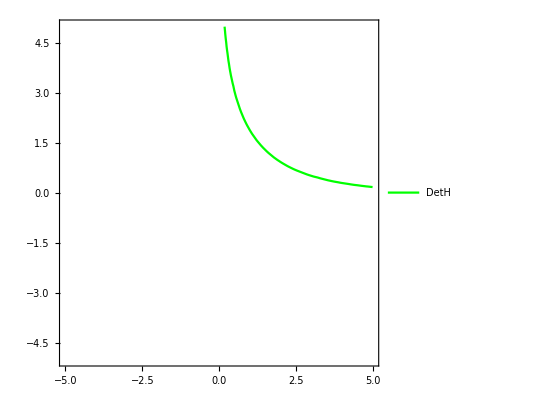

```mathematica
DetHeαCont=ContourPlot[DetHeαEva==0,{ze,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zα},-d+(2 (1-ⅇ^(-ze/2)) ((1-ⅇ^(-zα/2))/(1-ⅇ^-zα)-d h) k)/(1-ⅇ^-ze)>=0],ContourShading->None,ContourStyle->{Green},PlotLegends->{"DetH"}]
```

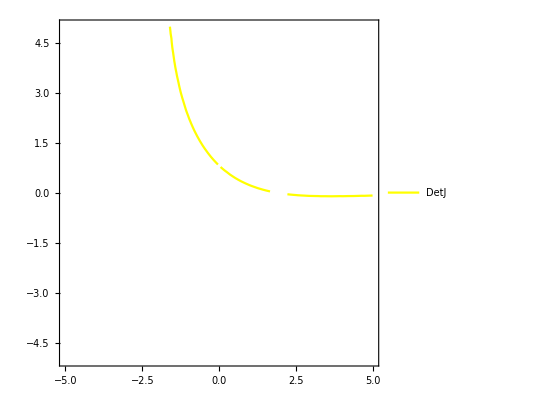

```mathematica
DetJeαCont=ContourPlot[DetJeαEva==0,{ze,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zα},-d+(2 (1-ⅇ^(-ze/2)) ((1-ⅇ^(-zα/2))/(1-ⅇ^-zα)-d h) k)/(1-ⅇ^-ze)>=0],ContourShading->None,ContourStyle->{Yellow},PlotLegends->{"DetJ"}]
```

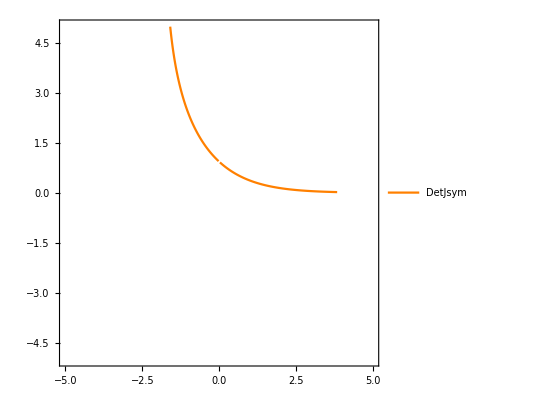

```mathematica
DetJsymeαCont=ContourPlot[DetJsymeαEva==0,{ze,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zα},-d+(2 (1-ⅇ^(-ze/2)) ((1-ⅇ^(-zα/2))/(1-ⅇ^-zα)-d h) k)/(1-ⅇ^-ze)>=0],ContourShading->None,ContourStyle->{Orange},PlotPoints->101,PlotLegends->{"DetJsym"}]
```

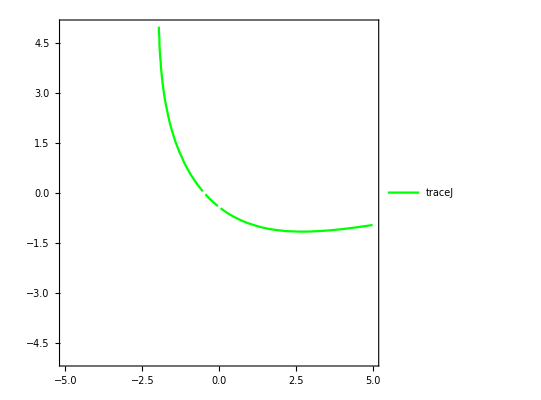

```mathematica
trJeαCont=ContourPlot[trJeαEva==0,{ze,-4.99,4.98},{zα,-4.99,4.98},ContourShading->None,ContourStyle->{Green},PlotLegends->{"traceJ"}]
```

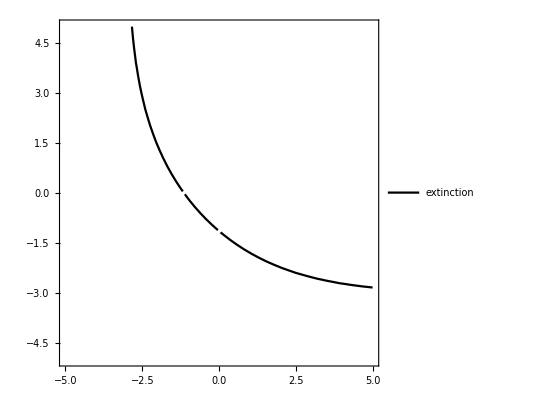

```mathematica
exConteα=ContourPlot[ConsExeαEva==0,{ze,-4.99,4.98},{zα,-4.99,4.98},ContourShading->None,ContourStyle->{Black},PlotLegends->{"extinction"}]
```

```mathematica
stabeαCont=ContourPlot[stabeα,{ze,-5,5},{zα,-5,5},Contours->{0},Exclusions->"Discontinuities",ContourShading->None,ContourStyle->{Yellow},PlotLegends->{"stability"}]
```

-Graphics-

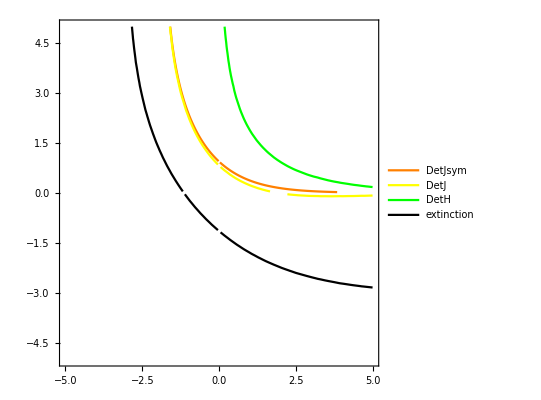

```mathematica
Show[DetJsymeαCont,DetJeαCont,DetHeαCont,exConteα] (* Figure E1a *)
```

## Joint evolution off handling time and conversion efficiency

### Analytical results

Invasion fitness

```mathematica
Sαh=S/.resαh
```

-d+(e R1[θα,θh] α1[θαm]+e R2[θα,θh] α2[θαm])/(1+e h1[θhm] R1[θα,θh]+e h2[θhm] R2[θα,θh])

Fitness gradient

```mathematica
D[Sαh,θαm]/.{θhm->θh,θαm->θα}//Simplify (* Eq. c11a *)
D[Sαh,θhm]/.{θhm->θh,θαm->θα}//Simplify  (* Eq. c11b *)
```

(e (R1[θα,θh] α1'[θα]+R2[θα,θh] α2'[θα]))/(1+e h1[θh] R1[θα,θh]+e h2[θh] R2[θα,θh])

-(e^2 (R1[θα,θh] α1[θα]+R2[θα,θh] α2[θα]) (R1[θα,θh] h1'[θh]+R2[θα,θh] h2'[θh]))/(1+e h1[θh] R1[θα,θh]+e h2[θh] R2[θα,θh])^2

Hessian

```mathematica
h11=D[Sαh,{θαm,2}];
h12=D[Sαh,θαm,θhm];
h22=D[Sαh,{θhm,2}];
{{h11,h12},{h12,h22}}/.sS/.singpt/.{R1[1/2,1/2]->R,R2[1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,r1->r,r2->r,k1->k,k2->k,α1'[1/2]->α',α2'[1/2]->-α',h1'[1/2]->h',h2'[1/2]->-h',α1''[1/2]->α'',α2''[1/2]->α'',h1''[1/2]->h'',h2''[1/2]->h''}//Simplify
```

{{(2 e R α'')/(1+2 e h R),0},{0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

```mathematica
Hαh={{(2 e R α'')/(1+2 e h R),0},{0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}; (* Eq. C12 *)
```

```mathematica
Det[Hαh]
```

-(8 e^3 R^3 α h'' α'')/(1+2 e h R)^3

```mathematica
DetHαh=-(8 e^3 R^3 α h'' α'')/(1+2 e h R)^3;
```

The denominator is negative. With this one can conclude that this expression is positive

Q-matrix

```mathematica
q11=D[Sαh,θαm,θα];
q12=D[Sαh,θαm,θh];
q21=D[Sαh,θhm,θα];
q22=D[Sαh,θhm,θh];
{{q11,q12},{q21,q22}}/.sS/.singpt/.{R1[1/2,1/2]->R,R2[1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,r1->r,r2->r,k1->k,k2->k,α1'[1/2]->α',α2'[1/2]->-α',h1'[1/2]->h',h2'[1/2]->-h',Derivative[1,0][R1][1/2,1/2]->Derivative[1,0][R],Derivative[1,0][R2][1/2,1/2]->Derivative[1,0][R],Derivative[0,1][R1][1/2,1/2]->Derivative[0,1][R],Derivative[0,1][R2][1/2,1/2]->Derivative[0,1][R]}//Simplify
```

{{0,0},{0,0}}

```mathematica
Qαh={{0,0},{0,0}};
```

Jacobian matrix

```mathematica
Jαh=Hαh+Qαh//Simplify
```

{{(2 e R α'')/(1+2 e h R),0},{0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

### Numerics

```mathematica
Clear[d,k,h,e]
```

```mathematica
DetHαh=-(8 e^3 R^3 α h'' α'')/(1+2 e h R)^3;
```

```mathematica
dh=D[th1,θh];
ddh=D[th1,θh,θh];
dα=D[tα1,θα];
ddα=D[tα1,θα,θα];
Rsym=R1/.EquilibPos[[1]]/.symParEcol/.symtraits//FullSimplify;
```

```mathematica
ConsExαhEva=2 e k(α-h d)-d/.TradeOffsHAsp/.singpt
DetHαhEva=DetHαh/.derivatives/.TradeOffsHAsp/.singpt;
```

-d+2 e ((1-ⅇ^(-zα/2))/(1-ⅇ^-zα)-d (1-(1-ⅇ^(-zh/2))/(1-ⅇ^-zh))) k

```mathematica
d=.9;k=2.5;e=1; (* parameters used for Figure E1b *)
```

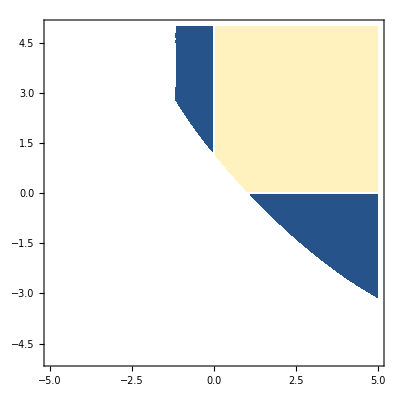

```mathematica
DetHαhCont=ContourPlot[DetHαhEva,{zα,-4.97,4.98},{zh,-4.97,4.98},Contours->{0},RegionFunction->Function[{zα,zh},-d+2 e ((1-ⅇ^(-zα/2))/(1-ⅇ^-zα)-d (1-(1-ⅇ^(-zh/2))/(1-ⅇ^-zh))) k>0],PlotLegends->{"DetH"}]
```

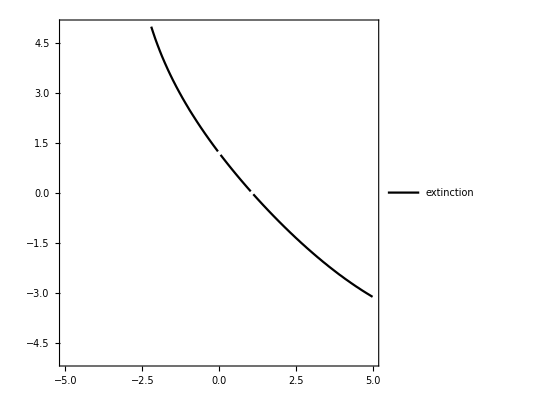

```mathematica
ConsExαhEvaCont=ContourPlot[ConsExαhEva==0,{zα,-4.99,4.98},{zh,-4.99,4.98},ContourShading->None,ContourStyle->{Black},PlotLegends->{"extinction"}]
```

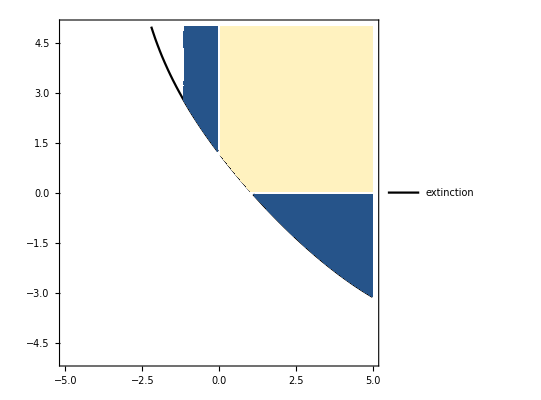

```mathematica
Show[ConsExαhEvaCont,DetHαhCont] (* Figure E1b *)
```

## Joint evolution of all three traits

### Analytical results

Invasion fitness

```mathematica
S
```

-d+(e1[θem] R1[θe,θh,θα] α1[θαm]+e2[θem] R2[θe,θh,θα] α2[θαm])/(1+e1[θem] h1[θhm] R1[θe,θh,θα]+e2[θem] h2[θhm] R2[θe,θh,θα])

Gradient

```mathematica
{D[S,θem],D[S,θhm],D[S,θαm]}/.sS//Simplify (* Eq. (C13) in the paper *)
```

{(R2[θe,θh,θα] α2[θα] e2'[θe]+R1[θe,θh,θα] (h1[θh] R2[θe,θh,θα] α2[θα] (-e2[θe] e1'[θe]+e1[θe] e2'[θe])+α1[θα] ((1+e2[θe] h2[θh] R2[θe,θh,θα]) e1'[θe]-e1[θe] h2[θh] R2[θe,θh,θα] e2'[θe])))/(1+e1[θe] h1[θh] R1[θe,θh,θα]+e2[θe] h2[θh] R2[θe,θh,θα])^2,-((e1[θe] R1[θe,θh,θα] α1[θα]+e2[θe] R2[θe,θh,θα] α2[θα]) (e1[θe] R1[θe,θh,θα] h1'[θh]+e2[θe] R2[θe,θh,θα] h2'[θh]))/(1+e1[θe] h1[θh] R1[θe,θh,θα]+e2[θe] h2[θh] R2[θe,θh,θα])^2,(e1[θe] R1[θe,θh,θα] α1'[θα]+e2[θe] R2[θe,θh,θα] α2'[θα])/(1+e1[θe] h1[θh] R1[θe,θh,θα]+e2[θe] h2[θh] R2[θe,θh,θα])}

Hessian matrix

```mathematica
h11=D[S,{θem,2}];
h12=D[S,θem,θαm];
h13=D[S,θem,θhm];
h22=D[S,{θαm,2}];
h23=D[S,θαm,θhm];
h33=D[S,{θhm,2}];
{{h11,h12,h13},{h12,h22,h23},{h13,h23,h33}}/.sS/.singpt/.{R1[1/2,1/2,1/2]->R,R2[1/2,1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,r1->r,r2->r,k1->k,k2->k,e1'[1/2]->e',e2'[1/2]->-e',α1'[1/2]->α',α2'[1/2]->-α',h1'[1/2]->h',h2'[1/2]->-h',e1''[1/2]->e'',e2''[1/2]->e'',α1''[1/2]->α'',α2''[1/2]->α'',h1''[1/2]->h'',h2''[1/2]->h''}//Simplify
```

{{(2 R α e'')/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R),-(4 e R^2 α e' h')/(1+2 e h R)^2},{(2 R e' α')/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(4 e R^2 α e' h')/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

```mathematica
H3D={{(2 R α e'')/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R),-(4 e R^2 α e' h')/(1+2 e h R)^2},{(2 R e' α')/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(4 e R^2 α e' h')/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
```

```mathematica
Det[H3D]//Simplify
```

(16 e^2 R^4 α (-e α e'' h'' α''+(e')^2 ((1+2 e h R) (α')^2 h''-2 e R α (h')^2 α'')))/(1+2 e h R)^5

```mathematica
DetHess3D=(16 e^2 R^4 α (-e α e'' h'' α''+(e')^2 ((1+2 e h R) (α')^2 h''-2 e R α (h')^2 α'')))/(1+2 e h R)^5;
```

Q-matrix

```mathematica
q11=D[S,θem,θe];
q12=D[S,θem,θα];
q13=D[S,θem,θh];
q21=D[S,θαm,θe];
q22=D[S,θαm,θα];
q23=D[S,θαm,θh];
q31=D[S,θhm,θe];
q32=D[S,θhm,θα];
q33=D[S,θhm,θh];
{{q11,q12,q13},{q21,q22,q23},{q31,q32,q33}}/.sS/.singpt/.{R1[1/2,1/2,1/2]->R,R2[1/2,1/2,1/2]->R,e1[1/2]->e,e2[1/2]->e,h1[1/2]->h,h2[1/2]->h, α1[1/2]->α, α2[1/2]->α,r1->r,r2->r,k1->k,k2->k,e1'[1/2]->e',e2'[1/2]->-e',α1'[1/2]->α',α2'[1/2]->-α',h1'[1/2]->h',h2'[1/2]->-h',Derivative[1,0,0][R1][1/2,1/2,1/2]->Derivative[1,0,0][R],Derivative[1,0,0][R2][1/2,1/2,1/2]->-Derivative[1,0,0][R],Derivative[0,1,0][R1][1/2,1/2,1/2]->Derivative[0,1,0][R],Derivative[0,1,0][R2][1/2,1/2,1/2]->Derivative[0,1,0][R],Derivative[0,0,1][R1][1/2,1/2,1/2]->Derivative[0,0,1][R],Derivative[0,0,1][R2][1/2,1/2,1/2]->Derivative[0,0,1][R]}//Simplify
```

{{(2 α e' R^(1,0,0))/(1+2 e h R)^2,0,0},{(2 e α' R^(1,0,0))/(1+2 e h R),0,0},{-(4 e^2 R α h' R^(1,0,0))/(1+2 e h R)^2,0,0}}

```mathematica
Q3D={{(2 α e' Derivative[1,0,0][R])/(1+2 e h R)^2,0,0},{(2 e α' Derivative[1,0,0][R])/(1+2 e h R),0,0},{-(4 e^2 R α h' Derivative[1,0,0][R])/(1+2 e h R)^2,0,0}};
```

Jacobian matrix

```mathematica
H3D+Q3D//Simplify
```

{{(2 α (R e''+e' R^(1,0,0)))/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R),-(4 e R^2 α e' h')/(1+2 e h R)^2},{(2 α' (R e'+e R^(1,0,0)))/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(4 e R α h' (R e'+e R^(1,0,0)))/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

```mathematica
J3D={{(2 α (R e''+e' Derivative[1,0,0][R]))/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R),-(4 e R^2 α e' h')/(1+2 e h R)^2},{(2 α' (R e'+e Derivative[1,0,0][R]))/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(4 e R α h' (R e'+e Derivative[1,0,0][R]))/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
```

We use the Routh-Hurwitz criteria to determine the sign of the real parts of the eigenvalues of the three-dimensional Jacobian matrix.

```mathematica
Clear[λ]
charpolJ3D=CharacteristicPolynomial[J3D,λ];
Coefficient[-charpolJ3D,λ,0]//Simplify  (* negative of determinant, coefficient of the constant term of the characteristic polynomial *)
Coefficient[-charpolJ3D,λ,1]//Simplify (* coefficient of the linear term of the characteristic polynomial *)
Coefficient[-charpolJ3D,λ,2]//Simplify (* negative of trace, coefficient of the quadratic term of the characteristic polynomial *)
Coefficient[-charpolJ3D,λ,3]//Simplify (* coefficient of the cubic term of the characteristic polynomial *)
```

(16 e^2 R^3 α (e R α e'' h'' α''-R (e')^2 ((1+2 e h R) (α')^2 h''-2 e R α (h')^2 α'')+e e' (-(1+2 e h R) (α')^2 h''+α (2 e R (h')^2+h'') α'') R^(1,0,0)))/(1+2 e h R)^5

-1/(1+2 e h R)^4 4 R (R (e')^2 (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2)+e R α (2 e^2 R (1+2 e h R) h'' α''+e'' (2 e R α h''-(1+2 e h R) α''))+e e' (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2+α (2 e R α h''-(1+2 e h R) α'')) R^(1,0,0))

-(2 (R α e''-2 e^2 R^2 α h''+e R α''+2 e^2 h R^2 α''+α e' R^(1,0,0)))/(1+2 e h R)^2

1

```mathematica
trJ3D=(2 (R α e''-2 e^2 R^2 α h''+e R α''+2 e^2 h R^2 α''+α e' Derivative[1,0,0][R]))/(1+2 e h R)^2; (* trace *)
a2J3D=-1/(1+2 e h R)^4 4 R (R (e')^2 (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2)+e R α (2 e^2 R (1+2 e h R) h'' α''+e'' (2 e R α h''-(1+2 e h R) α''))+e e' (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2+α (2 e R α h''-(1+2 e h R) α'')) Derivative[1,0,0][R]); (*  *)
DetJ3D=(16 e^2 R^3 α ((1+2 e h R) e' (α')^2 h'' (R e'+e Derivative[1,0,0][R])-2 e R α e' (h')^2 α'' (R e'+e Derivative[1,0,0][R])-e α h'' α'' (R e''+e' Derivative[1,0,0][R])))/(1+2 e h R)^5; (* determinant *)
```

Third Routh-Hurwitz condition (see p. 310 in Otto & Day, 2007).

```mathematica
-trJ3D a2J3D+DetJ3D//Simplify
```

1/(1+2 e h R)^6 8 R ((R α e''-2 e^2 R^2 α h''+e R α''+2 e^2 h R^2 α''+α e' R^(1,0,0)) (R (e')^2 (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2)+e R α (2 e^2 R (1+2 e h R) h'' α''+e'' (2 e R α h''-(1+2 e h R) α''))+e e' (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2+α (2 e R α h''-(1+2 e h R) α'')) R^(1,0,0))+2 e^2 R^2 (1+2 e h R) α ((1+2 e h R) e' (α')^2 h'' (R e'+e R^(1,0,0))-2 e R α e' (h')^2 α'' (R e'+e R^(1,0,0))-e α h'' α'' (R e''+e' R^(1,0,0))))

```mathematica
RH3D=1/(1+2 e h R)^6 8 R ((R α e''-2 e^2 R^2 α h''+e R α''+2 e^2 h R^2 α''+α e' Derivative[1,0,0][R]) (R (e')^2 (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2)+e R α (2 e^2 R (1+2 e h R) h'' α''+e'' (2 e R α h''-(1+2 e h R) α''))+e e' (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2+α (2 e R α h''-(1+2 e h R) α'')) Derivative[1,0,0][R])+2 e^2 R^2 (1+2 e h R) α ((1+2 e h R) e' (α')^2 h'' (R e'+e Derivative[1,0,0][R])-2 e R α e' (h')^2 α'' (R e'+e Derivative[1,0,0][R])-e α h'' α'' (R e''+e' Derivative[1,0,0][R])))
```

Symmetric Jacobian

```mathematica
(J3D+Transpose[J3D])/2//Simplify
```

{{(2 α (R e''+e' R^(1,0,0)))/(1+2 e h R)^2,(α' (2 R e'+e R^(1,0,0)))/(1+2 e h R),-(2 e R α h' (2 R e'+e R^(1,0,0)))/(1+2 e h R)^2},{(α' (2 R e'+e R^(1,0,0)))/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(2 e R α h' (2 R e'+e R^(1,0,0)))/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}}

```mathematica
Jsym3D={{(2 α (R e''+e' Derivative[1,0,0][R]))/(1+2 e h R)^2,(α' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R),-(2 e R α h' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R)^2},{(α' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(2 e R α h' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
```

```mathematica
Det[Jsym3D]//Simplify
```

(4 e^2 R^2 α ((1+2 e h R) (α')^2 h'' (2 R e'+e R^(1,0,0))^2-2 e R α (h')^2 α'' (2 R e'+e R^(1,0,0))^2-4 e R α h'' α'' (R e''+e' R^(1,0,0))))/(1+2 e h R)^5

```mathematica
DetJsym3D=(4 e^2 R^2 α ((1+2 e h R) (α')^2 h'' (2 R e'+e Derivative[1,0,0][R])^2-2 e R α (h')^2 α'' (2 R e'+e Derivative[1,0,0][R])^2-4 e R α h'' α'' (R e''+e' Derivative[1,0,0][R])))/(1+2 e h R)^5;
```

### Numerics

Summary of analytical results (needs to be evaluated for the numerical calculations)

```mathematica
H3D={{(2 R α e'')/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R),-(4 e R^2 α e' h')/(1+2 e h R)^2},{(2 R e' α')/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(4 e R^2 α e' h')/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
DetH3D=(16 e^2 R^4 α (-e α e'' h'' α''+(e')^2 ((1+2 e h R) (α')^2 h''-2 e R α (h')^2 α'')))/(1+2 e h R)^5;
Q3D={{(2 α e' Derivative[1,0,0][R])/(1+2 e h R)^2,0,0},{(2 e α' Derivative[1,0,0][R])/(1+2 e h R),0,0},{-(4 e^2 R α h' Derivative[1,0,0][R])/(1+2 e h R)^2,0,0}};
J3D={{(2 α (R e''+e' Derivative[1,0,0][R]))/(1+2 e h R)^2,(2 R e' α')/(1+2 e h R),-(4 e R^2 α e' h')/(1+2 e h R)^2},{(2 α' (R e'+e Derivative[1,0,0][R]))/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(4 e R α h' (R e'+e Derivative[1,0,0][R]))/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
DetJ3D=(16 e^2 R^3 α ((1+2 e h R) e' (α')^2 h'' (R e'+e Derivative[1,0,0][R])-2 e R α e' (h')^2 α'' (R e'+e Derivative[1,0,0][R])-e α h'' α'' (R e''+e' Derivative[1,0,0][R])))/(1+2 e h R)^5;
Jsym3D={{(2 α (R e''+e' Derivative[1,0,0][R]))/(1+2 e h R)^2,(α' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R),-(2 e R α h' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R)^2},{(α' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R),(2 e R α'')/(1+2 e h R),0},{-(2 e R α h' (2 R e'+e Derivative[1,0,0][R]))/(1+2 e h R)^2,0,-(4 e^2 R^2 α h'')/(1+2 e h R)^2}};
DetJsym3D=(4 e^2 R^2 α ((1+2 e h R) (α')^2 h'' (2 R e'+e Derivative[1,0,0][R])^2-2 e R α (h')^2 α'' (2 R e'+e Derivative[1,0,0][R])^2-4 e R α h'' α'' (R e''+e' Derivative[1,0,0][R])))/(1+2 e h R)^5;
trJ3D=(2 (R α e''-2 e^2 R^2 α h''+e R α''+2 e^2 h R^2 α''+α e' Derivative[1,0,0][R]))/(1+2 e h R)^2;
RH3D=1/(1+2 e h R)^6 8 R ((R α e''-2 e^2 R^2 α h''+e R α''+2 e^2 h R^2 α''+α e' Derivative[1,0,0][R]) (R (e')^2 (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2)+e R α (2 e^2 R (1+2 e h R) h'' α''+e'' (2 e R α h''-(1+2 e h R) α''))+e e' (4 e^2 R^2 α^2 (h')^2+(1+2 e h R)^2 (α')^2+α (2 e R α h''-(1+2 e h R) α'')) Derivative[1,0,0][R])+2 e^2 R^2 (1+2 e h R) α ((1+2 e h R) e' (α')^2 h'' (R e'+e Derivative[1,0,0][R])-2 e R α e' (h')^2 α'' (R e'+e Derivative[1,0,0][R])-e α h'' α'' (R e''+e' Derivative[1,0,0][R])));
```

#### Bifurcation plot (Figure 6 in the main part of the paper)

```mathematica
Clear[d,k]
```

```mathematica
de=D[te1,θe];
dde=D[te1,θe,θe];
dh=D[th1,θh];
ddh=D[th1,θh,θh];
dα=D[tα1,θα];
ddα=D[tα1,θα,θα];
Rsym=R1/.EquilibPos[[1]]/.symParEcol/.symtraits//FullSimplify;
R1=R1/.EquilibPos[[1]]/.symParEcol/.{e1->te1,e2->te2}/.symtraits//Simplify;
d1R=D[R1,θe]/.singpt//FullSimplify;
```

```mathematica
ConsExEva=2 e k(α-h d)-d/.TradeOffsEHAsp/.singpt//Simplify;
DetH3DEva=DetH3D/.derivatives/.TradeOffsEHAsp/.singpt//Simplify;
DetJsym3DEva=DetJsym3D/.derivatives/.TradeOffsEHAsp/.singpt//Simplify;
DetJ3DEva=DetJ3D/.derivatives/.TradeOffsEHAsp/.singpt//Simplify;
trJ3DEva=trJ3D/.derivatives/.TradeOffsEHAsp/.singpt//Simplify;
RH3DEva=RH3D/.derivatives/.TradeOffsEHAsp/.singpt;
```

```mathematica
d=.9;k=2.5;
```

```mathematica
DetH3DCont=ContourPlot3D[DetH3DEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},ContourStyle->{Green},PlotLegends->{"DetH"},AxesLabel->{"ze","zh","zα"},PlotPoints->20]
```

-Graphics3D-

```mathematica
DetJsym3DCont=ContourPlot3D[DetJsym3DEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},ContourStyle->{Orange},PlotLegends->{"DetJsym"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
DetJ3DCont=ContourPlot3D[DetJ3DEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},ContourStyle->{White},PlotLegends->{"DetJ"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
trJ3DCont=ContourPlot3D[trJ3DEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},ContourStyle->{Pink},PlotLegends->{"trJ"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
RH3DCont=ContourPlot3D[RH3DEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},ContourStyle->{Blue},PlotLegends->{"3rd Routh-Hurwitz"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
exCont=ContourPlot3D[ConsExEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},Contours->{0},ContourStyle->{White},PlotLegends->{"extinction"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
Show[DetH3DCont,DetJsym3DCont,DetJ3DCont,RH3DCont,trJ3DCont,exCont]
```

-Graphics3D-

This is Fig. 6 in the paper. Note, however, that from Fig. 6 we have omitted all surfaces below the extinction boundary and, for clarity, also the surface that indicate DetJ=0, trJ=0 and zero for the third Routh-Hurwitz condition.

#### Checking the branching conditions (i)-(v) of Geritz et al. (2016)

```mathematica
Clear[d,k]
```

```mathematica
de=D[te1,θe];
dde=D[te1,θe,θe];
dh=D[th1,θh];
ddh=D[th1,θh,θh];
dα=D[tα1,θα];
ddα=D[tα1,θα,θα];
Rsym=R1/.EquilibPos[[1]]/.symParEcol/.symtraits//FullSimplify;
R1=R1/.EquilibPos[[1]]/.symParEcol/.{e1->te1,e2->te2}/.symtraits//Simplify;
d1R=D[R1,θe]/.singpt//FullSimplify;
```

```mathematica
H3DEva=H3D/.derivatives/.TradeOffsEHAsp/.singpt//Simplify;
Q3DEva=Q3D/.derivatives/.TradeOffsEHAsp/.singpt//Simplify;
Jsym3DEva=Jsym3D/.derivatives/.TradeOffsEHAsp/.singpt//Simplify;
```

Here, we show in particular that (v) is fulfilled for strongly attracting and invadable singular points. We do this by checking condition (29) in Geritz et al. (2016).

```mathematica
Solve[{x u1,x u2,x u3}.{{q11,0,0},{q21,0,0},{q31,0,0}}.{x u1,x u2,x u3}==-2,x] (* Scaling factor of the eigenvector u3D corresponding to the dominant eigenvalue of the Hessian matrix H such that u3D.Q3DEvaEva.u3D)=-2. Here we choose the positive scaling factor. *)
```

{{x→-(√2)/(√(-q11 u1^2-q21 u1 u2-q31 u1 u3))},{x→(√2)/(√(-q11 u1^2-q21 u1 u2-q31 u1 u3))}}

```mathematica
Clear[k,d,ze,zh,zα]
```

```mathematica
Q3DEva
```

{{-0.997219,0,0},{-1.03883,0,0},{-0.934949,0,0}}

```mathematica
k=2.5;d=0.9;ze=0.7;zh=2;zα=2; (* example parameter set resulting in a strongly attracting singular point *)
H3DEva=H3D/.derivatives/.TradeOffsEHAsp/.singpt (* Hessian matrix. *)
EigenH=Eigensystem[H3DEva]
λ3D=Max[EigenH[[1]]] (* dominant eigenvalue of Hessian matrix *)
u3D=EigenH[[2,Ordering[EigenH[[1]],-1][[1]]]] (* eigenvector corresponding to dominant eigenvalue of Hessian matrix *)
Q3DEva=Q3D/.derivatives/.TradeOffsEHAsp/.singpt (* Q-matrix. *)
x=(√2)/(√(-Q3DEva[[1,1]] u3D[[1]]^2-Q3DEva[[2,1]] u3D[[1]]u3D[[2]]-Q3DEva[[3,1]] u3D[[1]]u3D[[3]])) (* scaling factor of the eigenvector corresponding to the dominant eigenvalue of the Hessian matrix H such that u3D.Q3DEvaEva.u3D)=-2 *)
u3Dscale=x u3D
Jsym3DEva=Jsym3D/.derivatives/.TradeOffsEHAsp/.singpt (* Symmetric part of the Jacobian matrix. *)
EigenJsym3D=Eigensystem[Jsym3DEva] (* Eigensystem of the symmetric part of the Jacobian matrix. *)
mMatrix=(IdentityMatrix[3]+( Q3DEva.Outer[Times,u3Dscale,u3Dscale])/2).(H3DEva+Q3DEva) (* Matrix described in the first line on p. 1093 of Geritz et al. (2016). *)
mu3D=Max[Eigensystem[mMatrix][[1]]] (* Dominant eigenvalue of the matrix described in the first line on p. 1093 of Geritz et al. (2016). *)
```

{{-0.703917,1.74981,1.57483},{1.74981,-2.09512,0},{1.57483,0,-1.8856}}

{{-3.7983,-1.97688,1.09054},{{-0.604847,0.621409,0.498007},{-0.0439505,-0.650464,0.758264},{-0.795128,-0.436747,-0.420743}}}

1.09054

{-0.795128,-0.436747,-0.420743}

{{-0.997219,0,0},{-1.03883,0,0},{-0.934949,0,0}}

1.23844

{-0.984718,-0.540885,-0.521065}

{{-1.70114,1.2304,1.10736},{1.2304,-2.09512,0},{1.10736,0,-1.8856}}

{{-3.51722,-1.97827,-0.186366},{{-0.672798,0.582101,0.45662},{-0.0626608,-0.659816,0.74881},{-0.737168,-0.475186,-0.480397}}}

{{-1.23118,1.4602,1.29583},{1.20055,-2.39682,-0.290645},{1.08049,-0.27153,-2.14719}}

0.

Checking the branching conditions (i)-(v) of Geritz et al. (2016) for strongly attracting singular points.

```mathematica
AllTrue[EigenJsym3D[[1]],Negative] (* Has to evaluate to True for the singular point to be strongly attracting (condition i). *)
AllTrue[EigenH[[1]],Negative] (* Has to evaluate to False for the singular point to be invadable (condition ii). *)
-u3D.Q3DEva.u3D>0 (* Has to evaluate to True for mutual invadability to be possible (condition iii). *)
mu3D<λ3D (* Second part of condition (29) in Geritz et al. (2016). Has to evaluate to True for condition (v) to be fulfilled. *)
```

True

False

True

True

Here, we show in particular that (v) is fulfilled for weakly attracting and invadable singular points for the case that the mutation variance-covariance matrix M equals the identity matrix.

```mathematica
Clear[k,d,ze,zh,zα]
```

```mathematica
k=2.5;d=0.9;ze=2;zh=0.4;zα=3;  (* Example parameter set resulting in a weakly attracting singular point. *)
H3DEva=H3D/.derivatives/.TradeOffsEHAsp/.singpt (* Hessian matrix. *)
EigenH=Eigensystem[H3DEva] (* Eigensystem of the Hessian matrix. *)
λ3D=Max[EigenH[[1]]] (* Dominant eigenvalue of Hessian matrix. *)
Q3DEva=Q3D/.derivatives/.TradeOffsEHAsp/.singpt (* Q-matrix. *)
DetJ3DEva=DetJ3D/.derivatives/.TradeOffsEHAsp/.singpt (* Determinant of the Jacobian. *)
DetJsym3DEva=DetJsym3D/.derivatives/.TradeOffsEHAsp/.singpt  (* Determinant of the symmetric part of the Jacobian. *)
u3D=EigenH[[2,Ordering[EigenH[[1]],-1][[1]]]] (* Eigenvector corresponding to dominant eigenvalue of Hessian matrix. *)
mMatrix=(IdentityMatrix[3]-(Q3DEva.Outer[Times,u3D,u3D])/(u3D.Q3DEva.u3D)).(H3DEva+Q3DEva) (* Matrix described in the first line on p. 1093 of Geritz et al. (2016). *)
mu3D=Max[Eigensystem[%][[1]]] (* Dominant eigenvalue of the matrix described in the first line on p. 1093 of Geritz et al. (2016). *)
```

{{-1.05688,0.902629,1.14552},{0.902629,-2.32646,0},{1.14552,0,-0.393664}}

{{-2.92831,-1.42513,0.576437},{{0.538108,-0.807029,-0.243195},{-0.555876,-0.556679,0.617341},{0.633594,0.19701,0.748162}}}

0.576437

{{-0.415202,0,0},{-0.609309,0,0},{-0.773268,0,0}}

-0.251927

0.132383

{0.633594,0.19701,0.748162}

{{-1.21457,0.853596,0.959311},{0.671216,-2.39841,-0.273258},{0.851833,-0.0913185,-0.740454}}

0.

Checking the branching conditions (i)-(v) of Geritz et al. (2016) for weakly attracting singular points.

```mathematica
DetJsym3DEva>0 ||DetJ3DEva<0(* Has to evaluate to True for the singular point to be weakly attracting (condition i). *)
AllTrue[EigenH[[1]],Negative] (* Has to evaluate to False for the singular point to be invadable (condition ii). *)
-u3D.Q3DEva.u3D>0 (* Has to evaluate to True for mutual invadability to be possible (condition iii). *)
mu3D<λ3D (* Second part of condition (29) in Geritz et al. (2016). Has to evaluate to True for condition (v) to be fulfilled. *)
```

True

False

True

True

Does evolutionary branching become more likely with an increasing number of jointly evolving traits?

In this section we produce the plots that are used to measure the proportions in the space of trade-off curvature parameters that lead to the different evolutionary outcomes when one, two or three traits evolve.

```mathematica
de=D[te1,θe];
dde=D[te1,θe,θe];
dh=D[th1,θh];
ddh=D[th1,θh,θh];
dα=D[tα1,θα];
ddα=D[tα1,θα,θα];
Rsym=R1/.EquilibPos[[1]]/.symParEcol/.symtraits//FullSimplify;
R1=R1/.EquilibPos[[1]]/.symParEcol/.{e1->te1,e2->te2}/.symtraits//Simplify;
d1R=D[R1,θe]/.singpt//FullSimplify;
```

#### Regions of trade-off curvatures resulting in different evolutionary outcomes when only e is evolving.

```mathematica
Clear[d,k]
```

```mathematica
He=(2 R α e'')/(1+2 e h R)^2; (* Hessian when only e is evolving *)
Je=(2 α (e' R'+R e''))/(1+2 e h R)^2;  (* Jacobian when only e is evolving *)
```

```mathematica
ConsExEva=2 e k(α-h d)-d/.derivatives/.TradeOffsEHAsp/.singpt; (* Existence region of the consumer *)
HeEva=He/.derivatives/.TradeOffsEHAsp/.singpt; (* Hessian *)
JeEva=Je/.derivatives/.TradeOffsEHAsp/.singpt; (* Jacobian *)
```

```mathematica
HeCont=ContourPlot3D[HeEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zh,zα},ConsExEva>=0],ContourStyle->{Green},PlotLegends->{"DetH"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
JeCont=ContourPlot3D[JeEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zh,zα},ConsExEva>=0], ContourStyle->{Orange},PlotLegends->{"DetJ"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
exCont=ContourPlot3D[ConsExEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},ContourStyle->{White},PlotLegends->{"extinction"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
Show[HeCont,JeCont,exCont]  (* Figure E6a *)
```

-Graphics3D-

```mathematica
Clear[ConsExEva,HeEva,JeEva]

ConsExEva[ze_,zh_,zα_]=2 e k(α-h d)-d/.derivatives/.TradeOffsEHAsp/.singpt; (* Coexistence region of the consumer *)
HeEva[ze_,zh_,zα_]=He/.derivatives/.TradeOffsEHAsp/.singpt;
JeEva[ze_,zh_,zα_]=Je/.derivatives/.TradeOffsEHAsp/.singpt;
```

```mathematica
totalVol=NIntegrate[Boole[ze>-4.99],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}](* consumer viable *)
viable=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}](* consumer viable *)
strongattr=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0&&JeEva[ze,zh,zα]<0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}] 
uninvadable=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0&&HeEva[ze,zh,zα]<0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

991.027

183.767

167.552

152.507

Area of in the space of trade-off curvature parameters in percent conditional on consumer population being viable (numbers in first column in Table 1)

```mathematica
repeller=(viable-strongattr) 100/viableVol
branching=(strongattr-uninvadable) 100/viableVol
endpoint=uninvadable 100/viableVol
```

8.82358

8.18707

82.9894

#### Regions of trade-off curvatures resulting in different evolutionary outcomes when e is evolving jointly with h.

```mathematica
Clear[d,k]
```

```mathematica
DetHeh=-(8 e^2 R^3 α^2 (2 R (e')^2 (h')^2+e'' h''))/(1+2 e h R)^4; (* Hessian when e and h are evolving *)
DetJsymeh=-(4 e^2 R^2 α^2 (4 R^2 (e')^2 (h')^2+2 R e'' h''+2 e' (2 e R (h')^2+h'') Derivative[1,0][R]+e^2 (h')^2 (Derivative[1,0][R])^2))/(1+2 e h R)^4; (* Symmetric part of the Jacobian when e and h are evolving *)
```

```mathematica
ConsExEva=2 e k(α-h d)-d/.TradeOffsEHAsp/.singpt;
DetHehEva=DetHeh/.derivatives/.TradeOffsEHAsp/.singpt;
DetJsymehEva=DetJsymeh/.derivatives/.TradeOffsEHAsp/.singpt;
```

```mathematica
d=.9;k=2.5;
```

```mathematica
DetHehCont=ContourPlot3D[DetHehEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zh,zα},ConsExEva>=0],ContourStyle->{Green},PlotLegends->{"DetH"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
DetJsymehCont=ContourPlot3D[DetJsymehEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zh,zα},ConsExEva>=0],ContourStyle->{Orange},PlotLegends->{"DetJsym"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
ConsExEva/.{ze->1,zh->1,zα->1}
exCont=ContourPlot3D[ConsExEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},ContourStyle->{White},PlotLegends->{"extinction"},AxesLabel->{"ze","zh","zα"}]
```

-0.0202386

-Graphics3D-

```mathematica
Show[DetHehCont,DetJsymehCont,exCont] (* Figure E6b *)
```

-Graphics3D-

```mathematica
Clear[ConsExEva,DetHehEva,DetJsymehEva]

ConsExEva[ze_,zh_,zα_]=2 e k(α-h d)-d/.TradeOffsEHAsp/.singpt;
DetHehEva[ze_,zh_,zα_]=DetHeh/.derivatives/.TradeOffsEHAsp/.singpt;
DetJsymehEva[ze_,zh_,zα_]=DetJsymeh/.derivatives/.TradeOffsEHAsp/.singpt;
```

```mathematica
totalVol=NIntegrate[Boole[ze>-4.99],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}](* consumer viable *)
viable=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}](* consumer viable *)
strongattr=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0&&DetJsymehEva[ze,zh,zα]>0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}] 
uninvadable=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0&&DetHehEva[ze,zh,zα]>0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

991.027

183.767

127.936

101.022

Area of in the space of trade-off curvature parameters in percent conditional on consumer population being viable (numbers in second column in Table 1)

```mathematica
repeller=(viable-strongattr) 100/viableVol
branching=(strongattr-uninvadable) 100/viableVol
endpoint=uninvadable 100/viableVol
```

30.3814

14.6458

54.9728

#### Regions of trade-off curvatures resulting in different evolutionary outcomes when all three traits are evolving.

```mathematica
Clear[d,k]
```

```mathematica
DetHehα=(16 e R^4 α (e (e')^2 (α')^2 h''+2 e^2 h R (e')^2 (α')^2 h''-2 e^2 R α (e')^2 (h')^2 α''-e^2 α e'' h'' α''))/(1+2 e h R)^5; (* determinant of Hessian when all three traits are evolving *)
DetJsymehα=1/(1+2 e h R)^5 2 e R α (-h' (2 R e'+e Derivative[1,0,0][R]) (8 e^2 R^3 α e' h' α''+4 e^3 R^2 α h' α'' Derivative[1,0,0][R])-2 e R h'' (-(1+2 e h R) (α')^2 (2 R e'+e Derivative[1,0,0][R])^2+4 e R α α'' (R e''+e' Derivative[1,0,0][R])));  (* determinant of Symmetric part of the Jacobian when all three traits are evolving *)
```

```mathematica
ConsExEva=2 e k(α-h d)-d/.TradeOffsEHAsp/.singpt;
DetHehαEva=DetHehα/.derivatives/.TradeOffsEHAsp/.singpt;
DetJsymehαEva=DetJsymehα/.derivatives/.TradeOffsEHAsp/.singpt;
```

```mathematica
d=0.9;k=2.5;
```

```mathematica
DetHehαCont=ContourPlot3D[DetHehαEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zh,zα},ConsExEva>=0],ContourStyle->{Green},PlotLegends->{"DetH"},AxesLabel->{"ze","zα","zh"},PlotPoints->20]
```

-Graphics3D-

```mathematica
DetJsymehαCont=ContourPlot3D[DetJsymehαEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},RegionFunction->Function[{ze,zh,zα},ConsExEva>=0],ContourStyle->{Orange},PlotLegends->{"DetJsym"},AxesLabel->{"ze","zα","zh"}]
```

-Graphics3D-

```mathematica
exCont=ContourPlot3D[ConsExEva==0,{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},Contours->{0},ContourStyle->{White},PlotLegends->{"extinction"},AxesLabel->{"ze","zh","zα"}]
```

-Graphics3D-

```mathematica
Show[DetHehαCont,DetJsymehαCont,exCont](* Figure 6 *)
```

-Graphics3D-

```mathematica
Clear[ConsExEva,DetHehαEva,DetJsymehαEva]

ConsExEva[ze_,zh_,zα_]=2 e k(α-h d)-d/.TradeOffsEHAsp/.singpt;
DetHehαEva[ze_,zh_,zα_]=DetHehα/.derivatives/.TradeOffsEHAsp/.singpt;
DetJsymehαEva[ze_,zh_,zα_]=DetJsymehα/.derivatives/.TradeOffsEHAsp/.singpt;
```

```mathematica
totalVol=NIntegrate[Boole[ze>-4.99],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}](* consumer viable *)
viable=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}](* consumer viable *)
strongattr=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0&&DetJsymehαEva[ze,zh,zα]<0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}] 
uninvadable=NIntegrate[Boole[ConsExEva[ze,zh,zα]>0&&DetHehαEva[ze,zh,zα]<0],{ze,-4.99,4.98},{zh,-4.99,4.98},{zα,-4.99,4.98},PrecisionGoal->10,MaxRecursion->40,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

991.027

183.767

56.3598

40.5179

Area of in the space of trade-off curvature parameters in percent conditional on consumer population being viable (numbers in third column in Table 1)

```mathematica
repeller=(viable-strongattr) 100/viableVol
branching=(strongattr-uninvadable) 100/viableVol
endpoint=uninvadable 100/viableVol
```

69.3308

8.62068

22.0486